# AMASeriesRepresentation Examples

## Model Component Validation

### getB, getF, getPhi, genx0z0Funcs, genX0Z0Funcs,checkLinMod,, checkMod

```mathematica
?getB
```

getB[linMod] B from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getF
```

getF[linMod] F from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getPhi
```

getPhi[linMod] Phi from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
Through[{getB,getF,getPhi}[notLinMod]]
```

{{{-0.0282384,-0.0552487,0.00939369},{-0.0664679,-0.700462,-0.0718527},{-0.163638,-1.39868,0.331726}},{{-0.381174,-0.223904,0.0940684},{-0.134352,-0.189653,0.630956},{-0.816814,-1.00033,0.0417094}},{{0.0210079,0.15727,-0.0531634},{1.20712,-0.0553003,-0.431842},{2.58165,-0.183521,-0.578227}}}

```mathematica
?genx0z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions x0(xtm1,eps) and z0(xtm1,eps)  based on the linear reference model

```mathematica
x0z0func=genx0z0Funcs[linMod] ;x0z0func @@ anXEpsFlat
```

{{0.392799},{0.20416},{1.10505},{0},{0},{0}}

```mathematica
?genX0Z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions  expected X0(xtm1) and Z0(xtm1)   based on the linear reference model

```mathematica
X0Z0func=genX0Z0Funcs[linMod];X0Z0func @@ anXFlat
```

{{0.389195},{0.202287},{1.09505},{0},{0},{0}}

```mathematica
?checkLinMod
```

checkLinMod[linMod,anX_?MatrixQ,anEps_?MatrixQ,numRegimes_Integer:0]
computes eigenvalues and checks consistency of dimensions of model components
returns {Eigenvalues[BB]//Abs,Eigenvalues[FF]//Abs,X0Z0 @@anX,lilxz @@Join[anX,anEps,Table[0,{numZ}]]}
numRegimes currently has no impact

```mathematica
checkLinMod[linMod,anX,anEps]
```

{{0.949953,0.36,0.},{0.342,0.,0.},{{0.389195},{0.202287},{1.09505},{0},{0},{0}},{{0.2},{0.18},{1.1},{0.392799},{0.20416},{1.10505},{0.407658},{0.211883},{1.09985},{0.01}}}

```mathematica
?genFRFunc
```

genFRFunc[{numX_Integer,numEps_Integer,numZ_Integer},
xkFunc:(_Function|_CompiledFunction),eqnsFunc:(_Function|_CompiledFunction)]

returns a function that uses FindRoot to solve the eqnsFunc system using the xkFuncs in the series approximation for the conditional expectations function

```mathematica
?checkMod
```

checkMod[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},anX_?MatrixQ,anEps_?MatrixQ,
eqnsFunc:(_Function|_CompiledFunction)]

```mathematica
checkMod[{genNSFunc},linMod,aGSpec,theDist,anX,{{0.7}},rbcEqnsFunctionalNext]
```

{{{0.2},{0.18},{1.1},{0.641468},{0.333407},{1.79571},{0.733403},{0.381191},{1.75594},{0.7}},{{0.754557},{0.434568},{2.2046},{0.627752},{-0.00948746},{0.408886}},{{0.754557},{0.434568},{2.2046},{0.627752},{-0.00948746},{0.408886}}}

```mathematica
checkMod[{genFRFunc},linMod,aGSpec,theDist,anX,{{0.7}},rbcEqnsFunctionalNext]
```

{{{0.2},{0.18},{1.1},{0.641468},{0.333407},{1.79571},{0.733403},{0.381191},{1.75594},{0.7}},{{0.754557},{0.434568},{2.2046},{0.627752},{-0.00948746},{0.408886}},{{0.754557},{0.434568},{2.2046},{0.627752},{-0.00948746},{0.408886}}}

```mathematica
checkMod[{genNSFunc},linMod,aGSpec,theDist,anX,{{0.7}},rbcEqnsFunctionalNext]
```

{{{0.2},{0.18},{1.1},{0.641468},{0.333407},{1.79571},{0.733403},{0.381191},{1.75594},{0.7}},{{0.754557},{0.434568},{2.2046},{0.627752},{-0.00948746},{0.408886}},{{0.754557},{0.434568},{2.2046},{0.627752},{-0.00948746},{0.408886}}}

### truncErrorMat

```mathematica
?truncErrorMat
```

truncErrorMat[{{fmat,_Real,2},{phimat,_Real,2},{kk,_Integer}}]

computes the truncation error matrix

```mathematica
truncErrorMat[getF[notLinMod],getPhi[notLinMod],3]
```

{{0.246116,-0.0114312,-0.0661884},{-0.00370631,0.058752,-0.0692077},{1.08452,-0.0635452,-0.272294}}

## Construct AMA Series Given a Solution Path or Given a Decision Rule (Both Perfect Foresight and Rational Expectations)

### genZsFromPath

```mathematica
?genZsFromPath
```

genZsFromPath[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
thePath_?MatrixQ,theEps_?MatrixQ]

    given the path
	computes the z values using the hmat in linMod
	returns a list of z matrices(one column matrices)

```mathematica
iterateDRREIntegrate[simpRBCExactDR,anXEps,theDist,6]
```

{{0.2},{0.18},{1.1},{0.392455},{0.203981},{1.10577},{0.408491},{0.212316},{1.10028},{0.412468},{0.214383},{1.09509},{0.412055},{0.214168},{1.09018},{0.410152},{0.213179},{1.08554},{0.407812},{0.211963},{1.08115}}

```mathematica
sip=genZsFromPath[linMod,iterateDRREIntegrate[simpRBCExactDR,anXEps,theDist,6],anXEps[[{-1}]]]
```

{{{0.00615901},{-0.000915881},{0.000718209}},{{0.00671986},{0.00121583},{-0.000246413}},{{0.00611557},{0.00132655},{-0.000221425}},{{0.00548079},{0.00120726},{-0.000198992}},{{0.00491736},{0.00108195},{-0.000178848}}}

### iterateDRREIntegrate

```mathematica
?iterateDRREIntegrate
```

iterateDRREIntegrate[drFunc:(_Function|_CompiledFunction),initVec_?MatrixQ,
	distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},numPers_Integer]
	
Iterates a decision rule forward from initVec(includes time zero shocks) for numPers time intervals by integrating out the shocks 
using the distribution
and, if not {},the regime change transition probablities

produces a matrix containing the path

```mathematica
kip=iterateDRREIntegrate[simpRBCExactDR,anXEps,theDist,2]
```

{{0.2},{0.18},{1.1},{0.392455},{0.203981},{1.10577},{0.408491},{0.212316},{1.10028}}

```mathematica
kip=iterateDRREIntegrate[simpRBCExactDR,anXEps,theDist,5]
```

{{0.2},{0.18},{1.1},{0.392455},{0.203981},{1.10577},{0.408491},{0.212316},{1.10028},{0.412468},{0.214383},{1.09509},{0.412055},{0.214168},{1.09018},{0.410152},{0.213179},{1.08554}}

### genZsREExact

```mathematica
?genZsREExact
```

genZsREExact[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},theExactDR:(_Function|_CompiledFunction),iters_Integer]
	
	iterates a decision rule forward using iterateDRIntegrate (can use PerfectForesight as distribution for specific shocks)
	computes the z values using the hmat in linMod
	returns a list of z matrices(one column matrices)

```mathematica
rip=genZsREExact[linMod,anXEps,theDist,simpRBCExactDR,5]
```

{{{0.00615901},{-0.000915881},{0.000718209}},{{0.00671986},{0.00121583},{-0.000246413}},{{0.00611557},{0.00132655},{-0.000221425}},{{0.00548079},{0.00120726},{-0.000198992}},{{0.00491736},{0.00108195},{-0.000178848}}}

### genASeriesRep

```mathematica
?genASeriesRep
```

genASeriesRep[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	initVec_?MatrixQ,theZs:{_?MatrixQ..},len_Integer]
	
matrix of the  values for {xtm1,xt,xtp1,eps} from the series representations using 
from the first len z matrices

```mathematica
rip=genZsREExact[linMod,anXEps,theDist,simpRBCExactDR,5];trySer=genASeriesRep[linMod,anXEps,rip,5]
```

{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}}

```mathematica
sip=genZsFromPath[linMod,iterateDRREIntegrate[simpRBCExactDR,anXEps,theDist,6],anXEps[[{-1}]]];
trySer=genASeriesRep[linMod,anXEps,sip,5]
```

{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}}

```mathematica
sip
```

{{{0.00615901},{-0.000915881},{0.000718209}},{{0.00671986},{0.00121583},{-0.000246413}},{{0.00611557},{0.00132655},{-0.000221425}},{{0.00548079},{0.00120726},{-0.000198992}},{{0.00491736},{0.00108195},{-0.000178848}}}

### genSeriesReps

```mathematica
?genSeriesReps
```

genSeriesReps[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},theExactDR:(_Function|_CompiledFunction),maxIters_Integer]
	
generates  Zs using genZsREExact, then uses genASeriesRep to generate a list of the possible  values for {xtm1,xt,xtp1,eps} from the series representations using 
from just the first z matrix to all the z's

```mathematica
arbMod=genSeriesReps[linMod,anXEps,theDist,simpRBCExactDR,5]
```

{{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}},{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}},{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}},{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}},{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}}}

### genSeriesRepFunc

```mathematica
?genSeriesRepFunc
```

genSeriesRepFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},theExactDR:(_Function|_CompiledFunction),terms_Integer]
	
generates  Zs using genZsREExact, then 
returns a function that 
uses genASeriesRep to generate the value for  {xtm1,xt,xtp1,eps} from the the series representation with the given number of terms

```mathematica
arbModFunc=genSeriesRepFunc[linMod,theDist,simpRBCExactDR,5];
arbModFunc@@anXEps
```

{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}}

## Evaluate Solution Path Errors

### evalPathErrDRREIntegrate

```mathematica
?evalPathErrDRREIntegrate
```

evalPathErrDRREIntegrate[drFunc_Function,initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction)]

uses decision rule to compute an unconditional expectations path of length 2, then applies eqnsFunc 
returns a  vector of equations errors

```mathematica
evalPathErrDRREIntegrate[simpRBCExactDR,anXEps,theDist,rbcEqnsFunctionalNext]
```

{{0.},{1.11022×10^-16},{0.}}

```mathematica
evalPathErrDRREIntegrate[simpRBCExactDR,anXEps,theDist,rbcEqnsFunctionalNext]
```

{{0.},{1.11022×10^-16},{0.}}

### pathErrsDRREIntegrate

```mathematica
?pathErrsDRREIntegrate
```

pathErrsDRREIntegrate[drFunc_Function,initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction),numPers_Integer]

uses decision rule to compute an unconditional expectations path of length numPers, then applies eqnsFunc along the path
returns List of vectors of equations errors

```mathematica
pathErrsDRREIntegrate[simpRBCExactDR,anXEps,theDist,rbcEqnsFunctionalNext,8]
```

{{{0.},{1.11022×10^-16},{0.}},{{1.33227×10^-15},{1.11022×10^-16},{0.0000550128}},{{-4.44089×10^-16},{4.44089×10^-16},{0.0000547533}},{{-4.44089×10^-16},{0.},{0.0000545079}},{{-8.88178×10^-16},{2.22045×10^-16},{0.0000542758}},{{-8.88178×10^-16},{-1.11022×10^-16},{0.0000540562}},{{0.},{-1.11022×10^-16},{0.0000538484}}}

```mathematica
pathErrsDRREIntegrate[simpRBCExactDR,anXEps,theDist,rbcEqnsFunctionalNext,8]
```

{{{0.},{1.11022×10^-16},{0.}},{{1.33227×10^-15},{1.11022×10^-16},{0.0000550128}},{{-4.44089×10^-16},{4.44089×10^-16},{0.0000547533}},{{-4.44089×10^-16},{0.},{0.0000545079}},{{-8.88178×10^-16},{2.22045×10^-16},{0.0000542758}},{{-8.88178×10^-16},{-1.11022×10^-16},{0.0000540562}},{{0.},{-1.11022×10^-16},{0.0000538484}}}

### evalBadPathErrDRREIntegrate

```mathematica
?evalBadPathErrDRREIntegrate
```

evalBadPathErrDRREIntegrate[drFunc_Function,noEpsVec_?MatrixQ,
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction)]

given the initial state vector and the decision rule uses FindMaximum to find the time t shock that produces the largest infinity norm for the error in the
system equations
returns the infintiy norm of the error and the shock value

```mathematica
evalBadPathErrDRREIntegrate[simpRBCExactDR,Drop[anXEps,-1],theDist,rbcEqnsFunctionalNext]
```

{4.44089×10^-16,{eVs129→0.}}

### worstPathForErrDRREIntegrate

```mathematica
?worstPathForErrDRREIntegrate
```

worstPathForErrDRREIntegrate[drFunc_Function,noEpsVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction)]

returns the path corresponding to evalBadPathErrDRREIntegrate

```mathematica
worstPathForErrDRREIntegrate[simpRBCExactDR,Drop[anXEps,-1],theDist,rbcEqnsFunctionalNext]
```

{{0.2},{0.18},{1.1},{0.38855},{0.201952},{1.09477},{0.403175},{0.209553},{1.08988},{0.}}

```mathematica
worstPathForErrDRREIntegrate[simpRBCExactDR,Drop[anXEps,-1],theDist,rbcEqnsFunctionalNext]
```

{{0.2},{0.18},{1.1},{0.38855},{0.201952},{1.09477},{0.403175},{0.209553},{1.08988},{0.}}

### genErrsREWorst

```mathematica
?genErrsREWorst
```

genErrsREWorst[theDRFunc:(_Function|_CompiledFunction),initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},
	theSysFunc:(_Function|_CompiledFunction),iters_Integer]
	
	iterates the decision rule using iterateDRREIntegrate
	applies worstPathForErrDRREIntegrate all along the path to return a list of
	vectors corresponding to maximum infinity norm errors in the sysFunc equations

```mathematica
genErrsREWorst[simpRBCExactDR,anXEps,theDist,rbcEqnsFunctionalNext,2]
```

done thePath

done worstPaths{{{0.392455},{0.203981},{1.10577},{0.408471},{0.212306},{1.10023},{0.412441},{0.214369},{1.09504},{-3.15406×10^-10}},{{0.408491},{0.212316},{1.10028},{0.412448},{0.214373},{1.09504},{0.412028},{0.214154},{1.09013},{1.74829×10^-8}},{{0.412468},{0.214383},{1.09509},{0.412034},{0.214157},{1.09013},{0.410125},{0.213165},{1.08549},{-1.39935×10^-10}}}{1,2,3}

{{{-1.33227×10^-15},{1.11022×10^-16},{0.}},{{1.77636×10^-15},{1.11022×10^-16},{0.}},{{-8.88178×10^-16},{0.},{0.}}}

```mathematica
Head[rbcEqnsFunctionalNext]
```

CompiledFunction

```mathematica
Get["AMASeriesRepresentation`"];
```

reading AMASeriesRepresentation`

changing MatrixPower to produce Identity Matrix for singular matrices raised to 0th power

genNSRegimeFuncs not implemented

done reading AMASeriesRepresentation`

```mathematica
Get["betterQuasiRBC`"]
```

computing steady state subs

RE done now PF

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

RE solutions

computing and simplifying the symbolic b phi f etc

```mathematica
anX0Z0=genX0Z0Funcs[linModBetterQuasi];
lilxkzk=genLilXkZkFunc[linModBetterQuasi,{anX0Z0,2},anX0Z0@@anXFlatBetterQuasi,{{{1,2}},rbcEqnsFunctionBetterQuasi}]
```

Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},{xxxtm1Var$4},{xxxtm1Var$5},{-0.129747+0.692632 xxxtm1Var$2+0.360048 xxxtm1Var$5-0.0444237 zzz$0$1+0.658 zzz$0$2},{-0.0674368+0.36 xxxtm1Var$2+0.187137 xxxtm1Var$5+0.0444237 zzz$0$1+0.342 zzz$0$2},{0.+1. zzz$0$5},{6.54814-5.33229 xxxtm1Var$2-2.77186 xxxtm1Var$5+0.342 zzz$0$1-5.06568 zzz$0$2+1. zzz$0$3},{0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$5+1. zzz$0$4},{-0.129747+0.692632 (-0.0674368+0.36 xxxtm1Var$2+0.187137 xxxtm1Var$5+0.0444237 zzz$0$1+0.342 zzz$0$2)+0.360048 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$5+1. zzz$0$4)},{-0.0674368+0.36 (-0.0674368+0.36 xxxtm1Var$2+0.187137 xxxtm1Var$5+0.0444237 zzz$0$1+0.342 zzz$0$2)+0.187137 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$5+1. zzz$0$4)},{0.},{6.54814-5.33229 (-0.0674368+0.36 xxxtm1Var$2+0.187137 xxxtm1Var$5+0.0444237 zzz$0$1+0.342 zzz$0$2)-2.77186 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$5+1. zzz$0$4)},{0.0500976+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$5+1. zzz$0$4)},{epsVar$1}}]

```mathematica
anX0Z0@@anXFlatBetterQuasi
```

{{0.390979},{0.203214},{0.},{2.53928},{1.09505},{0},{0},{0},{0},{0}}

## Construct Solution Decision Rule Series Components

### makeDREvalInterp, doIterREInterp, nestIterREInterp

### makeDREvalInterp

```mathematica
?makeInterpFunc
```

makeInterpFunc[aVecFunc_Function,
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0}]

returns an interpolating function based on the vector function and grid specification

```mathematica
tryFunc=Function[{ww,yy,zz,xx},{{Sin[xx]*yy*E^zz},{xx+yy/zz},{99*zz}}];huh=makeInterpFunc[tryFunc,aGSpec];huh[2,.2,1,.01]
```

{{0.00543949},{0.210222},{99.}}

```mathematica
?makeDREvalInterp
```

makeDREvalInterp[drFunc_Function,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},
eqnsFunc:(_Function|_CompiledFunction),gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0}]

returns a list of two functions: the first evaluates the error in the equations without interpolation, the second uses interpolation

```mathematica
{ theNotInterp,theInterp}=makeDREvalInterp[simpRBCExactDR,theDist,rbcEqnsFunctionalNext,aGSpec];
```

```mathematica
{theInterp @@ anXEpsFlat,theNotInterp @@ anXEpsFlat}
```

{{{-4.96059×10^-16},{0.},{0.}},{{0.},{1.11022×10^-16},{0.}}}

### fSum, fSumC

```mathematica
?fSum
```

fSum[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	{},
	xtGuess_?MatrixQ]

returns matrix of the F weigthed sum of z's

```mathematica
anX0Z0=genX0Z0Funcs[linMod];{nxtxz,nxtXZ}=doIterREInterp[{genFRFunc},linMod,{anX0Z0,1},rbcEqnsFunctionalNext,aGSpec,theDist];
```

```mathematica
lilxkzk=genLilXkZkFunc[linMod,{nxtXZ,2},(anX0Z0@@anXFlat)[[Range[3]]]]
```

Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},{-0.111693+0.36039 epsVar$1+0.692632 xxxtm1Var$2+0.342028 xxxtm1Var$3-0.0444237 zzz$0$1+0.658 zzz$0$2+0.360048 zzz$0$3},{-0.0580784+0.187315 epsVar$1+0.36 xxxtm1Var$2+0.177771 xxxtm1Var$3+0.0444237 zzz$0$1+0.342 zzz$0$2+0.187137 zzz$0$3},{0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$3+1. zzz$0$3},{-0.111682+0.692632 (-0.0580784+0.187315 epsVar$1+0.36 xxxtm1Var$2+0.177771 xxxtm1Var$3+0.0444237 zzz$0$1+0.342 zzz$0$2+0.187137 zzz$0$3)+0.342028 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$3+1. zzz$0$3)},{-0.0573349+0.36 (-0.0580784+0.187315 epsVar$1+0.36 xxxtm1Var$2+0.177771 xxxtm1Var$3+0.0444237 zzz$0$1+0.342 zzz$0$2+0.187137 zzz$0$3)+0.177771 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$3+1. zzz$0$3)},{0.0500367+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$3+1. zzz$0$3)},{epsVar$1}}]

```mathematica
nxtXZ @@ anXFlat
```

{{0.37777},{0.195827},{1.09497},{-0.00772797},{-0.0178449},{-0.0000749254}}

```mathematica
anX0Z0@@anXFlat
```

{{0.389195},{0.202287},{1.09505},{0},{0},{0}}

```mathematica
lilxkzk @@anXEpsZsFlat
```

{{0.2},{0.18},{1.1},{0.627988},{0.333127},{1.40505},{0.59962},{0.312369},{1.38477},{0.01}}

```mathematica
fSum[linMod,{nxtXZ,7},anX]
```

{{-0.0123996},{-0.00548627},{-0.0000749254}}

```mathematica
?fSumC
```

fSumC=Compile[{{phi,_Real,2},{FF,_Real,2},{psiZ,_Real,2},{zPath,_Real,3}},...]


returns matrix of the F weigthed sum of z's

```mathematica
rip=genZsREExact[linMod,anXEps,theDist,simpRBCExactDR,5];
fSumC[getB[linMod],getF[linMod],IdentityMatrix[3],rip]
```

{{0.000050454},{-0.000641214},{0.000682265}}

### compareFormula, genPathCompare

```mathematica
?compareFormula
```

compareFormula[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	{XZFunc_Function,numSteps_Integer},xtm1Vars_?MatrixQ,epsVars_?MatrixQ,xtztVal_?MatrixQ]

```mathematica
anX0Z0=genX0Z0Funcs[linMod];compareFormula[linMod,{anX0Z0,5},anX,anEps,Drop[anXEpsZs,{4}]]
```

{{0.2},{0.18},{1.1},{0.627971},{0.333144},{1.40505},{0.599605},{0.311649},{1.38483},{0.01}}

### genLilXkZkFunc

```mathematica
?genLilXkZkFunc
```

genLilXkZkFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	XZFuncs:({_Function,_Integer}),xtGuess_?MatrixQ]

uses the guess to compute the F sum in AMA series expansion
returns a function	(xtm1,eps,zvars) that returns a vector of{xtm1,xt,xtp1,eps) values

```mathematica
anX0Z0=genX0Z0Funcs[linMod];
lilxkzk=genLilXkZkFunc[linMod,{anX0Z0,3},anX0Z0@@ anXEpsFlat];
```

```mathematica
lilxkzk
```

Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},{-0.111709+0.36039 epsVar$1+0.692632 xxxtm1Var$2+0.342028 xxxtm1Var$3-0.0444237 zzz$0$1+0.658 zzz$0$2+0.360048 zzz$0$3},{-0.0580617+0.187315 epsVar$1+0.36 xxxtm1Var$2+0.177771 xxxtm1Var$3+0.0444237 zzz$0$1+0.342 zzz$0$2+0.187137 zzz$0$3},{0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$3+1. zzz$0$3},{-0.111709+0.692632 (-0.0580617+0.187315 epsVar$1+0.36 xxxtm1Var$2+0.177771 xxxtm1Var$3+0.0444237 zzz$0$1+0.342 zzz$0$2+0.187137 zzz$0$3)+0.342028 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$3+1. zzz$0$3)},{-0.0580617+0.36 (-0.0580617+0.187315 epsVar$1+0.36 xxxtm1Var$2+0.177771 xxxtm1Var$3+0.0444237 zzz$0$1+0.342 zzz$0$2+0.187137 zzz$0$3)+0.177771 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$3+1. zzz$0$3)},{0.0500976+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$3+1. zzz$0$3)},{epsVar$1}}]

```mathematica
lilxkzk@@ anXEpsZsFlat//InputForm
```

{{0.2}, {0.18}, {1.1}, {0.62797107309957}, {0.33314357748469003}, {1.4050548271635828}, 
 {0.5996046692205815}, {0.3116486274672324}, {1.384832918713013}, {0.01}}

```mathematica
With[{better=Flatten[nxtxz @@ anXEpsZsFlat]},{lilxkzk @@ anXEpsZsFlat,better,lilxkzk @@ Flatten[Join[better[[{1,2,3}]],anEps,better[[{4,5,6}]]]]}]
```

{{{0.2},{0.18},{1.1},{0.627971},{0.333144},{1.40505},{0.599605},{0.311649},{1.38483},{0.01}},{0.381458,0.197797,1.10577,-0.00692871,-0.018097,0.000718209},{{0.381458},{0.197797},{1.10577},{0.395759},{0.205231},{1.11126},{0.410521},{0.213371},{1.10574},{0.01}}}

### genFRFunc

```mathematica
?genFRFunc
```

genFRFunc[{numX_Integer,numEps_Integer,numZ_Integer},
xkFunc:(_Function|_CompiledFunction),eqnsFunc:(_Function|_CompiledFunction)]

returns a function that uses FindRoot to solve the eqnsFunc system using the xkFuncs in the series approximation for the conditional expectations function

```mathematica
anX0Z0=genX0Z0Funcs[linMod];
lilxkzk=genLilXkZkFunc[linMod,{anX0Z0,1},anX0Z0@@ anXEpsFlat];
frf=genFRFunc[{3,1,3},lilxkzk,rbcEqnsFunctionalNext];
frf @@ anXEpsFlat
```

{{0.392189},{0.204248},{1.10577},{0.00599681},{-0.000915881},{0.000718209}}

### genFPFunc

```mathematica
?genFPFunc
```

genFPFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
XZFuncs:({_Function,_Integer}),eqnsFunc:(_Function|_CompiledFunction)]

returns a function (xtm1,eps) by  iterating  to get  the correct value of xt (zt) to use in the conditional expectations function and iterates until the guess is consitent with the root finding solution

```mathematica
anX0Z0=genX0Z0Funcs[linMod];
lilxkzk=genLilXkZkFunc[linMod,{anX0Z0,2},anX0Z0@@anXEpsFlat];
anX0Z0=genX0Z0Funcs[linMod];
{nxtxz,nxtXZ}=doIterREInterp[{genFRFunc},linMod,{anX0Z0,2},rbcEqnsFunctionalNext,aGSpec,theDist];
thisOne=genXZFuncREInterp[{3,1,3},nxtxz,aGSpec,theDist];
```

```mathematica
fpf=genFPFunc[{genFRFunc},linMod,{thisOne,2},rbcEqnsFunctionalNext];
```

```mathematica
fpf @@ anXEpsFlat
```

InterpolatingFunction::dmval: Input value {0.205154,1.10577} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.392135},{0.204301},{1.10577},{0.00595345},{-0.000915881},{0.000718209}}

```mathematica
thisOne  @@ anXFlat
```

{{0.37777},{0.195827},{1.09497},{-0.00772797},{-0.0178449},{-0.0000749254}}

```mathematica
?genPathCompare
```

genPathCompare[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	xzFunc_Function,{XZFunc_Function,numSteps_Integer},xtm1Val_?MatrixQ,epsVal_?MatrixQ]

```mathematica
anx0z0=genx0z0Funcs[linMod];anX0Z0=genX0Z0Funcs[linMod];
genPathCompare[linMod,anx0z0,{anX0Z0,2},anX,anEps]
```

{{{0.2},{0.18},{1.1},{0.407658},{0.211883},{1.09985},{0.411226},{0.213738},{1.0949},{0.410819},{0.213526},{1.0902}},{{0.2},{0.18},{1.1},{0.392799},{0.20416},{1.10505},{0.407658},{0.211883},{1.09985},{0.01}}}

```mathematica
?doIterREInterp
```

doIterREInterp[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	XZFuncsNow:{(_Function|_InterpolatingFunction|_CompiledFunction),_Integer},
eqnsFunc:(_Function|_CompiledFunction),gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]




given a reference linear model, (x,z,X,Z) function and  and equation system
extends (x,z,X,Z) an additional period imposing rational expectations using interpolation to avoid recalculation of all the points along the path

returns a pair of functions xz and XZ giving the xt values of x and z and giving the unconditional expected path of future values of x and z

```mathematica
??doIterREInterp
```

doIterREInterp[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	XZFuncsNow:{(_Function|_InterpolatingFunction|_CompiledFunction),_Integer},
eqnsFunc:(_Function|_CompiledFunction),gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]




given a reference linear model, (x,z,X,Z) function and  and equation system
extends (x,z,X,Z) an additional period imposing rational expectations using interpolation to avoid recalculation of all the points along the path

returns a pair of functions xz and XZ giving the xt values of x and z and giving the unconditional expected path of future values of x and z

doIterREInterp[AMASeriesRepresentation`Private`theSolver:{genFRFunc,AMASeriesRepresentation`Private`opts:OptionsPattern[]}|{genNSFunc,AMASeriesRepresentation`Private`opts:OptionsPattern[]}|{specialSolver,AMASeriesRepresentation`Private`opts:OptionsPattern[]},AMASeriesRepresentation`Private`linMod:{AMASeriesRepresentation`Private`theHMat_?MatrixQ,AMASeriesRepresentation`Private`BB_?MatrixQ,AMASeriesRepresentation`Private`phi_?MatrixQ,AMASeriesRepresentation`Private`FF_?MatrixQ,AMASeriesRepresentation`Private`psiEps_?MatrixQ,AMASeriesRepresentation`Private`psiC_?MatrixQ,AMASeriesRepresentation`Private`psiZ_?MatrixQ,AMASeriesRepresentation`Private`psiZPreComp_?MatrixQ},AMASeriesRepresentation`Private`XZFuncsNow:{_Function|_InterpolatingFunction|_CompiledFunction,_Integer},AMASeriesRepresentation`Private`eqnsFunc:_Function|_CompiledFunction,AMASeriesRepresentation`Private`gSpec:{AMASeriesRepresentation`Private`toIgnore:{_Integer...},AMASeriesRepresentation`Private`iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},AMASeriesRepresentation`Private`numRegimes_:0},AMASeriesRepresentation`Private`distribSpec:{AMASeriesRepresentation`Private`expctSpec:{{_Symbol,_}..},AMASeriesRepresentation`Private`regimeTransProbFunc_:{}}]:=With[{AMASeriesRepresentation`Private`numX=Length[AMASeriesRepresentation`Private`BB],AMASeriesRepresentation`Private`numEps=Length[AMASeriesRepresentation`Private`psiEps⟦1⟧],AMASeriesRepresentation`Private`numZ=Length[AMASeriesRepresentation`Private`psiZ⟦1⟧]},With[{AMASeriesRepresentation`Private`theFuncs=makeInterpFunc[genFPFunc[AMASeriesRepresentation`Private`theSolver,AMASeriesRepresentation`Private`linMod,AMASeriesRepresentation`Private`XZFuncsNow,AMASeriesRepresentation`Private`eqnsFunc],AMASeriesRepresentation`Private`gSpec]},{AMASeriesRepresentation`Private`theFuncs,genXZREInterpFunc[{AMASeriesRepresentation`Private`numX,AMASeriesRepresentation`Private`numEps,AMASeriesRepresentation`Private`numZ},AMASeriesRepresentation`Private`theFuncs,AMASeriesRepresentation`Private`gSpec,AMASeriesRepresentation`Private`distribSpec]}]]
 
doIterREInterp[Private`linMod:{Private`theHMat_?MatrixQ,Private`BB_?MatrixQ,Private`phi_?MatrixQ,Private`FF_?MatrixQ,Private`psiEps_?MatrixQ,Private`psiC_?MatrixQ,Private`psiZ_?MatrixQ,Private`psiZPreComp_?MatrixQ},Private`XZFuncsNow:{_Function|_InterpolatingFunction|_CompiledFunction,_Integer},Private`eqnsFunc:_Function|_CompiledFunction,Private`gSpec:{Private`toIgnore:{_Integer...},Private`iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},Private`numRegimes_:0},Private`distribSpec:{Private`expctSpec:{{_Symbol,_}..},Private`regimeTransProbFunc_:{}}]:=With[{Private`numX=Length[Private`BB],Private`numEps=Length[Private`psiEps⟦1⟧],Private`numZ=Length[Private`psiZ⟦1⟧]},With[{Private`theFuncs=makeInterpFunc[genFPFunc[Private`linMod,Private`XZFuncsNow,Private`eqnsFunc],Private`gSpec]},{Private`theFuncs,genXZFuncREInterp[{Private`numX,Private`numEps,Private`numZ},Private`theFuncs,Private`gSpec,Private`distribSpec]}]]

```mathematica
{nxtxz,nxtXZ}=doIterREInterp[{genFRFunc},linMod,{genX0Z0Funcs[linMod],2},rbcEqnsFunctionalNext,aGSpec,theDist];
{nxtxz @@anXEpsFlat,nxtXZ @@  anXEpsFlat}
```

{{{0.381458},{0.197797},{1.10577},{-0.00692871},{-0.018097},{0.000718209}},{{0.37777},{0.195827},{1.09497},{-0.00772797},{-0.0178449},{-0.0000749254}}}

```mathematica
?nestIterREInterp
```

nestIterREInterp[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
{XZFuncNow:(_Function|_InterpolatingFunction|_CompiledFunction),numTerms_Integer},eqnsFunc:(_Function|_CompiledFunction),
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},numIters_Integer]

recursively apply doIterREInterp numIters times

```mathematica
aBunchREInterp=nestIterREInterp[{genFRFunc},linMod,{anX0Z0,2},rbcEqnsFunctionalNext,aGSpec,theDist,2];
```

InterpolatingFunction::dmval: Input value {0.0833902,0.878014} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
{aBunchREInterp[[-1,1]] @@anXEpsFlat,aBunchREInterp[[-1,2]] @@anXEpsFlat}
```

{{{0.379344},{0.199911},{1.10577},{-0.0279317},{-0.018097},{0.000718209}},{{0.375737},{0.19786},{1.09497},{-0.0284174},{-0.0178449},{-0.0000749254}}}

### genXZFuncRE, genXZFuncREInterp

```mathematica
?genXZFuncRE
```

genXZFuncRE[{numX_Integer,ignored_Integer,numZ_Integer},
aLilXkZkFunc_Function,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]


given problem dimensions and xz functions 
returns  perfect foresight version functions for future unconditional expectations using interpolation to avoid recalculating all values along the path

```mathematica
?genXZFuncREInterp
```

genXZFuncREInterp[probDims:{numX_Integer,numEps_Integer,numZ_Integer},
aLilXkZkFunc_Function,gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]


given problem dimensions and xz functions 
returns  retional expectations version functions for future unconditional expectations using interpolation to avoid recalculating all values along the path

```mathematica
{nxtxz,nxtXZ}=doIterREInterp[{genFRFunc},linMod,{genX0Z0Funcs[linMod],2},rbcEqnsFunctionalNext,aGSpec,theDist];
thisOne=genXZFuncREInterp[{3,1,3},nxtxz,aGSpec,theDist];
Through[{thisOne,nxtXZ}@@#&[anXEpsFlat]]
```

{{{0.37777},{0.195827},{1.09497},{-0.00772797},{-0.0178449},{-0.0000749254}},{{0.37777},{0.195827},{1.09497},{-0.00772797},{-0.0178449},{-0.0000749254}}}

## Evaluate AMASeries Paths

### genPath, pathErrs

```mathematica
?genPath
```

genPath[xzFunc_Function,
{XZFunc_Function,numSteps_Integer},xtm1Val_?MatrixQ,epsVal_?MatrixQ]

generate a path using the xz and XZ funcs

returns a matrix of the path values

```mathematica
anX0Z0=genX0Z0Funcs[linMod];anx0z0=genx0z0Funcs[linMod];genPath[anx0z0,{anX0Z0,5},anX,{{0.01}}]
```

{{0.2},{0.18},{1.1},{0.407658},{0.211883},{1.09985},{0.411226},{0.213738},{1.0949},{0.410819},{0.213526},{1.0902},{0.409065},{0.212614},{1.08574},{0.406906},{0.211492},{1.0815},{0.404679},{0.210335},{1.07747}}

```mathematica
?pathErrs
```

pathErrs[{numX_Integer,numEps_Integer,numZs_Integer},
{lilXZFunc_Function,bigXZFuncs:{XZFunc_Function,numSteps_Integer}},eqnsFunc:(_Function|_CompiledFunction),
anX_?MatrixQ,anEps_?MatrixQ,X0Z0_Function]
 compute a path
returns a matrix of equation errors along the path

```mathematica
anX0Z0=genX0Z0Funcs[linMod];anx0z0=genx0z0Funcs[linMod];
pathErrs[{3,1,3},{anx0z0,{anX0Z0,10}},rbcEqnsFunctionalNext,anX,{{0.01}},anX0Z0]
```

{{-0.00516945,0.0263013,-0.00592587},{-0.00470389,-0.00131703,0.000274229}}

## Regime Switching

### makeRegimeFunc

```mathematica
fCon=fSum[linModBetter,{genX0Z0Funcs[linModBetter],2},anXEpsBetter]
```

{{0.},{0.},{0.},{0.}}

```mathematica
grub=AMASeriesRepresentation`Private`genFullVecVars[linModBetter,1]
```

{{{rgm456}},{{rgm457}},{{rgm458}},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},{xxxtm1Var$4}},{{epsVar$1}},{{zzz$0$1},{zzz$0$2},{zzz$0$3},{zzz$0$4}}}

```mathematica
AMASeriesRepresentation`Private`makeFullVec[Sequence @@ grub,linModBetter,#]&/@{fCon,fCon}
```

{{{rgm456},{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},{xxxtm1Var$4},{rgm457},{-0.129747+0.692632 xxxtm1Var$2+0.360048 xxxtm1Var$4-0.0444237 zzz$0$1+0.658 zzz$0$2},{-0.0674368+0.36 xxxtm1Var$2+0.187137 xxxtm1Var$4+0.0444237 zzz$0$1+0.342 zzz$0$2},{6.54814-5.33229 xxxtm1Var$2-2.77186 xxxtm1Var$4+0.342 zzz$0$1-5.06568 zzz$0$2+1. zzz$0$3},{0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$4+1. zzz$0$4},{rgm458},{-0.129747+0.692632 (-0.0674368+0.36 xxxtm1Var$2+0.187137 xxxtm1Var$4+0.0444237 zzz$0$1+0.342 zzz$0$2)+0.360048 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$4+1. zzz$0$4)},{-0.0674368+0.36 (-0.0674368+0.36 xxxtm1Var$2+0.187137 xxxtm1Var$4+0.0444237 zzz$0$1+0.342 zzz$0$2)+0.187137 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$4+1. zzz$0$4)},{6.54814-5.33229 (-0.0674368+0.36 xxxtm1Var$2+0.187137 xxxtm1Var$4+0.0444237 zzz$0$1+0.342 zzz$0$2)-2.77186 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$4+1. zzz$0$4)},{0.0500976+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$4+1. zzz$0$4)},{epsVar$1}},{{rgm456},{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},{xxxtm1Var$4},{rgm457},{-0.129747+0.692632 xxxtm1Var$2+0.360048 xxxtm1Var$4-0.0444237 zzz$0$1+0.658 zzz$0$2},{-0.0674368+0.36 xxxtm1Var$2+0.187137 xxxtm1Var$4+0.0444237 zzz$0$1+0.342 zzz$0$2},{6.54814-5.33229 xxxtm1Var$2-2.77186 xxxtm1Var$4+0.342 zzz$0$1-5.06568 zzz$0$2+1. zzz$0$3},{0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$4+1. zzz$0$4},{rgm458},{-0.129747+0.692632 (-0.0674368+0.36 xxxtm1Var$2+0.187137 xxxtm1Var$4+0.0444237 zzz$0$1+0.342 zzz$0$2)+0.360048 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$4+1. zzz$0$4)},{-0.0674368+0.36 (-0.0674368+0.36 xxxtm1Var$2+0.187137 xxxtm1Var$4+0.0444237 zzz$0$1+0.342 zzz$0$2)+0.187137 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$4+1. zzz$0$4)},{6.54814-5.33229 (-0.0674368+0.36 xxxtm1Var$2+0.187137 xxxtm1Var$4+0.0444237 zzz$0$1+0.342 zzz$0$2)-2.77186 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$4+1. zzz$0$4)},{0.0500976+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$4+1. zzz$0$4)},{epsVar$1}}}

```mathematica
fCon=fSum[linModBetter,{genX0Z0Funcs[linModBetter],2},anXEpsBetter];hoo=AMASeriesRepresentation`Private`genLilXkZkRegimeFuncs[linModBetter,{{genX0Z0Funcs[linModBetter],2},{genX0Z0Funcs[linModBetter],2}},anXEpsBetter];
```

```mathematica
hoo[[1]] @@Join[{0},anXEpsZsFlatBetter]
```

{{0},{0.2},{0.18},{1.},{1.1},{0},{0.518137},{0.276056},{1.86034},{1.50505},{rgm461},{0.60335},{0.313595},{0.904321},{1.47983},{0.01}}

```mathematica
boo=AMASeriesRepresentation`Private`genLilXkZkRegimeFuncs[linModBetter,{fCon,fCon}];
```

```mathematica
rbcEqnsFunctionalBetterRSRBC @@Flatten[hoo[[2]] @@Join[{0},anXEpsZsFlatBetter]]
```

{Function[{betterRSRBC`Private`rgmtm1,betterRSRBC`Private`cctm1,betterRSRBC`Private`kktm1,betterRSRBC`Private`nltm1,betterRSRBC`Private`thtm1,betterRSRBC`Private`rgmt,betterRSRBC`Private`cct,betterRSRBC`Private`kkt,betterRSRBC`Private`nlt,betterRSRBC`Private`tht,betterRSRBC`Private`rgmtp1,betterRSRBC`Private`cctp1,betterRSRBC`Private`kktp1,betterRSRBC`Private`nltp1,betterRSRBC`Private`thtp1,betterRSRBC`Private`epsVal},{1/(betterRSRBC`Private`cct)-(171 betterRSRBC`Private`nltp1 betterRSRBC`Private`tht)/(500 (betterRSRBC`Private`kkt)^(16/25)),betterRSRBC`Private`cct+betterRSRBC`Private`kkt-(betterRSRBC`Private`kktm1)^(9/25) betterRSRBC`Private`thtm1,-1/(betterRSRBC`Private`cct)+betterRSRBC`Private`nlt,betterRSRBC`Private`tht-2 ⅇ^(betterRSRBC`Private`epsVal) (betterRSRBC`Private`thtm1)^(19/20)}],Function[{betterRSRBC`Private`rgmtm1,betterRSRBC`Private`cctm1,betterRSRBC`Private`kktm1,betterRSRBC`Private`nltm1,betterRSRBC`Private`thtm1,betterRSRBC`Private`rgmt,betterRSRBC`Private`cct,betterRSRBC`Private`kkt,betterRSRBC`Private`nlt,betterRSRBC`Private`tht,betterRSRBC`Private`rgmtp1,betterRSRBC`Private`cctp1,betterRSRBC`Private`kktp1,betterRSRBC`Private`nltp1,betterRSRBC`Private`thtp1,betterRSRBC`Private`epsVal},{1/(betterRSRBC`Private`cct)-(171 betterRSRBC`Private`nltp1 betterRSRBC`Private`tht)/(500 (betterRSRBC`Private`kkt)^(16/25)),betterRSRBC`Private`cct+betterRSRBC`Private`kkt-(betterRSRBC`Private`kktm1)^(9/25) betterRSRBC`Private`thtm1,-1/(betterRSRBC`Private`cct)+betterRSRBC`Private`nlt,betterRSRBC`Private`tht-2 ⅇ^(betterRSRBC`Private`epsVal) (betterRSRBC`Private`thtm1)^(19/20)}]}[0,0.2,0.18,1.,1.1,1,0.518137,0.276056,1.86034,1.50505,rgm461,0.60335,0.313595,0.904321,1.47983,0.01]

```mathematica
haha=AMASeriesRepresentation`Private`genFRRegimeFuncs[{4,1,4},hoo,rbcEqnsFunctionalBetterRSRBC];
```

```mathematica
haha[[2]] @@ Join[{0},anXEpsFlatBetter]
```

{{1},{0.562486},{0.0308364},{1.77782},{2.21155},{-3.87361},{-0.000870847},{0.558907},{1.10649}}

```mathematica
haha[[1]] @@ Join[{0},anXEpsFlatBetter]
```

{{0},{0.562486},{0.0308364},{1.77782},{2.21155},{-3.87361},{-0.000870847},{0.558907},{1.10649}}

```mathematica
nana=AMASeriesRepresentation`Private`genFRRegimeFuncs[{4,1,4},hoo,rbcEqnsFunctionalBetterRSRBC];
```

```mathematica
dana=AMASeriesRepresentation`Private`genNSRegimeFuncs[{4,1,4},hoo,rbcEqnsFunctionalBetterRSRBC];
```

```mathematica
{nana[[1]] @@ Join[{1},anXEpsFlatBetter],nana[[2]] @@ Join[{0},anXEpsFlatBetter]}
```

{{{0},{0.562486},{0.0308364},{1.77782},{2.21155},{-3.87361},{-0.000870847},{0.558907},{1.10649}},{{1},{0.562486},{0.0308364},{1.77782},{2.21155},{-3.87361},{-0.000870847},{0.558907},{1.10649}}}

```mathematica
{dana[[1]] @@ Join[{1},anXEpsFlatBetter],dana[[2]] @@ Join[{0},anXEpsFlatBetter]}
```

{{{0},{-0.285233},{0.878556},{-3.5059},{2.21155},{15.209},{-0.000870847},{-11.2511},{1.10649}},{{1},{-0.285233},{0.878556},{-3.5059},{2.21155},{15.209},{-0.000870847},{-11.2511},{1.10649}}}

```mathematica
{dana[[2]] @@ Join[{1},anXEpsFlatBetter],nana[[2]] @@ Join[{0},anXEpsFlatBetter]}
```

{{{1},{-0.285233},{0.878556},{-3.5059},{2.21155},{15.209},{-0.000870847},{-11.2511},{1.10649}},{{1},{0.562486},{0.0308364},{1.77782},{2.21155},{-3.87361},{-0.000870847},{0.558907},{1.10649}}}

```mathematica
vana=AMASeriesRepresentation`Private`genFPRegimeFuncs[linModBetter,{{genX0Z0Funcs[linModBetter],2},{genX0Z0Funcs[linModBetter],2}},rbcEqnsFunctionalBetterRSRBC];
```

```mathematica
vana@@ Join[{0},anXEpsFlatBetter]
```

infp:{{{0.368827},{0.1917},{2.70982},{1.00005},{0},{0},{0},{0}},Function,{0,0.2,0.18,1.,1.1,0.01}}

infp:{{{0.368827},{0.1917},{2.70982},{1.00005},{0},{0},{0},{0}},Function,{0,0.2,0.18,1.,1.1,0.01}}

infp:{{{0.368827},{0.1917},{2.70982},{1.00005},{0},{0},{0},{0}},Function,{0,0.2,0.18,1.,1.1,0.01}}

«1 more identical outputs»

{{{0},{0.562486},{0.0308364},{1.77782},{2.21155},{-3.87361},{-0.000870847},{0.558907},{1.10649}},{{1},{0.562486},{0.0308364},{1.77782},{2.21155},{-3.87361},{-0.000870847},{0.558907},{1.10649}}}

```mathematica
vana@@ Join[{0},anXEpsFlatBetter+.02]
```

infp:{{{0.389881},{0.202643},{2.54774},{1.01905},{0},{0},{0},{0}},Function,{0,0.22,0.2,1.02,1.12,0.03}}

infp:{{{0.389881},{0.202643},{2.54774},{1.01905},{0},{0},{0},{0}},Function,{0,0.22,0.2,1.02,1.12,0.03}}

infp:{{{0.389881},{0.202643},{2.54774},{1.01905},{0},{0},{0},{0}},Function,{0,0.22,0.2,1.02,1.12,0.03}}

«1 more identical outputs»

{{{0},{0.61545},{0.0120137},{1.62483},{2.29518},{-4.56016},{0.00127438},{0.813662},{1.1511}},{{1},{0.61545},{0.0120137},{1.62483},{2.29518},{-4.56016},{0.00127438},{0.813662},{1.1511}}}

## betterRBC Model Component Validation

### getB, getF, getPhi, genx0z0Funcs, genX0Z0Funcs,checkLinMod,, checkMod

```mathematica
?getB
```

getB[linMod] B from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getF
```

getF[linMod] F from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getPhi
```

getPhi[linMod] Phi from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
Through[{getB,getF,getPhi}[linModBetter]]
```

{{{0.,0.692632,0.,0.360048},{0.,0.36,0.,0.187137},{0.,-5.33229,0.,-2.77186},{0.,0.,0.,0.949953}},{{0.,0.,-0.0444237,0.},{0.,0.,0.0444237,0.},{0.,0.,0.342,0.},{0.,0.,0.,0.}},{{-0.0444237,0.658,0.,0.},{0.0444237,0.342,0.,0.},{0.342,-5.06568,1.,0.},{0.,0.,0.,1.}}}

```mathematica
?genx0z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions x0(xtm1,eps) and z0(xtm1,eps)  based on the linear reference model

```mathematica
anXEpsFlatBetter
```

{0.2,0.18,1.,1.1,0.01}

```mathematica
x0z0func=genx0z0Funcs[linModBetter] ;x0z0func @@ anXEpsFlatBetter
```

{{0.390979},{0.203214},{2.53928},{1.10505},{0},{0},{0},{0}}

```mathematica
?genX0Z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions  expected X0(xtm1) and Z0(xtm1)   based on the linear reference model

```mathematica
X0Z0func=genX0Z0Funcs[linModBetter];X0Z0func @@ anXFlatBetter
```

{{0.390979},{0.203214},{2.53928},{1.09505},{0},{0},{0},{0}}

```mathematica
?checkLinMod
```

checkLinMod[linMod,anX_?MatrixQ,anEps_?MatrixQ,numRegimes_Integer:0]
computes eigenvalues and checks consistency of dimensions of model components
returns {Eigenvalues[BB]//Abs,Eigenvalues[FF]//Abs,X0Z0 @@anX,lilxz @@Join[anX,anEps,Table[0,{numZ}]]}
numRegimes currently has no impact

```mathematica
checkLinMod[linModBetter,anXBetter,anEpsBetter]
```

{{0.949953,0.36,0.,0.},{0.342,0.,0.,0.},{{0.390979},{0.203214},{2.53928},{1.09505},{0},{0},{0},{0}},{{0.2},{0.18},{1.},{1.1},{0.390979},{0.203214},{2.53928},{1.10505},{0.408878},{0.212517},{2.40148},{1.09985},{0.01}}}

```mathematica
?checkMod
```

checkMod[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},anX_?MatrixQ,anEps_?MatrixQ,
eqnsFunc:(_Function|_CompiledFunction)]

```mathematica
checkMod[linModBetter,aGSpecBetter,theDistBetter,anXBetter,{{0.7}},rbcEqnsFunctionalNextBetter]
```

{{{0.2},{0.18},{1.},{1.1},{0.390979},{0.203214},{2.53928},{1.79571},{0.657547},{0.341765},{0.48708},{1.75594},{0.7}},{{1.15824},{0.0308812},{1.9034},{2.2046},{-8.45944},{0.594931},{5.27098},{0.408886}},{{1.15824},{0.0308812},{1.9034},{2.2046},{-8.45944},{0.594931},{5.27098},{0.408886}}}

### truncErrorMat

```mathematica
?truncErrorMat
```

truncErrorMat[{{fmat,_Real,2},{phimat,_Real,2},{kk,_Integer}}]

computes the truncation error matrix

```mathematica
truncErrorMat[getF[notLinMod],getPhi[notLinMod],3]
```

{{0.246116,-0.0114312,-0.0661884},{-0.00370631,0.058752,-0.0692077},{1.08452,-0.0635452,-0.272294}}

## betterRBC Construct AMA Series Given a Solution Path or Given a Decision Rule (Both Perfect Foresight and Rational Expectations)

### genZsFromPath

```mathematica
?genZsFromPath
```

genZsFromPath[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
thePath_?MatrixQ,theEps_?MatrixQ]

    given the path
	computes the z values using the hmat in linMod
	returns a list of z matrices(one column matrices)

```mathematica
iterateDRREIntegrate[simpRBCExactDRBetter,anXEpsBetter,theDist,6]
```

{{0.2},{0.18},{1.},{1.1},{0.392455},{0.203981},{2.81758},{1.10577},{0.408491},{0.212316},{2.69353},{1.10028},{0.412468},{0.214383},{2.65497},{1.09509},{0.412055},{0.214168},{2.64573},{1.09018},{0.410152},{0.213179},{2.64669},{1.08554},{0.407812},{0.211963},{2.6511},{1.08115}}

```mathematica
sip=genZsFromPath[linMod,iterateDRREIntegrate[simpRBCExactDRBetter,anXEpsBetter,theDistBetter,6],anXEpsBetter[[{-1}]]]
```

{{{16.8099},{1.38855},{-0.806078}},{{-11.6255},{3.4839},{0.164621}},{{20.7142},{1.337},{0.662138}},{{7.69275},{-3.46402},{1.55966}},{{15.7058},{1.36147},{-2.35803}},{{-10.4028},{3.27493},{0.156604}},{{20.2384},{1.31549},{0.64582}}}

```mathematica
"
```

### iterateDRREIntegrate

```mathematica
?iterateDRREIntegrate
```

iterateDRREIntegrate[drFunc:(_Function|_CompiledFunction),initVec_?MatrixQ,
	distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},numPers_Integer]
	
Iterates a decision rule forward from initVec(includes time zero shocks) for numPers time intervals by integrating out the shocks 
using the distribution
and, if not {},the regime change transition probablities

produces a matrix containing the path

```mathematica
kip=iterateDRREIntegrate[simpRBCExactDRBetter,anXEpsBetter,theDistBetter,2]
```

{{0.2},{0.18},{1.},{1.1},{0.392455},{0.203981},{2.81758},{1.10577},{0.408491},{0.212316},{2.69353},{1.10028}}

```mathematica
kip=iterateDRREIntegrate[simpRBCExactDRBetter,anXEpsBetter,theDistBetter,5]
```

{{0.2},{0.18},{1.},{1.1},{0.392455},{0.203981},{2.81758},{1.10577},{0.408491},{0.212316},{2.69353},{1.10028},{0.412468},{0.214383},{2.65497},{1.09509},{0.412055},{0.214168},{2.64573},{1.09018},{0.410152},{0.213179},{2.64669},{1.08554}}

### genZsREExact

```mathematica
?genZsREExact
```

genZsREExact[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},theExactDR:(_Function|_CompiledFunction),iters_Integer]
	
	iterates a decision rule forward using iterateDRIntegrate (can use PerfectForesight as distribution for specific shocks)
	computes the z values using the hmat in linMod
	returns a list of z matrices(one column matrices)

```mathematica
rip=genZsREExact[linModBetter,anXEpsBetter,theDistBetter,simpRBCExactDRBetter,5]
```

{{{-0.298128},{0.00224304},{0.289663},{0.000718209}},{{-0.288799},{-0.00178822},{0.289069},{-0.000246413}},{{-0.276191},{-0.00151349},{0.281133},{-0.000221425}},{{-0.262396},{-0.00147837},{0.268702},{-0.000198992}},{{-0.248668},{-0.00145825},{0.255009},{-0.000178848}}}

### genASeriesRep

```mathematica
?genASeriesRep
```

genASeriesRep[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	initVec_?MatrixQ,theZs:{_?MatrixQ..},len_Integer]
	
matrix of the  values for {xtm1,xt,xtp1,eps} from the series representations using 
from the first len z matrices

```mathematica
rip=genZsREExact[linModBetter,anXEpsBetter,theDistBetter,simpRBCExactDRBetter,5];trySer=genASeriesRep[linModBetter,anXEpsBetter,rip,5]
```

{{0.2},{0.18},{1.},{1.1},{0.393388},{0.203049},{2.8104},{1.10577},{0.410649},{0.213208},{2.67751},{1.10125},{0.01}}

```mathematica
sip=genZsFromPath[linModBetter,iterateDRREIntegrate[simpRBCExactDRBetter,anXEpsBetter,theDistBetter,6],anXEpsBetter[[{-1}]]];
trySer=genASeriesRep[linModBetter,anXEpsBetter,sip,5]
```

{{0.2},{0.18},{1.},{1.1},{0.393388},{0.203049},{2.8104},{1.10577},{0.410649},{0.213208},{2.67751},{1.10125},{0.01}}

### genSeriesReps

```mathematica
?genSeriesReps
```

genSeriesReps[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},theExactDR:(_Function|_CompiledFunction),maxIters_Integer]
	
generates  Zs using genZsREExact, then uses genASeriesRep to generate a list of the possible  values for {xtm1,xt,xtp1,eps} from the series representations using 
from just the first z matrix to all the z's

```mathematica
arbMod=genSeriesReps[linModBetter,anXEpsBetter,theDistBetter,simpRBCExactDRBetter,12]
```

{{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}}}

```mathematica
simpRBCExactDRBetter@@ anXEpsFlatBetter
```

{{0.392455},{0.203981},{2.81758},{1.10577}}

### genSeriesRepFunc

```mathematica
?genSeriesRepFunc
```

genSeriesRepFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},theExactDR:(_Function|_CompiledFunction),terms_Integer]
	
generates  Zs using genZsREExact, then 
returns a function that 
uses genASeriesRep to generate the value for  {xtm1,xt,xtp1,eps} from the the series representation with the given number of terms

```mathematica
arbModFunc=genSeriesRepFunc[linModBetter,theDistBetter,simpRBCExactDRBetter,5];
arbModFunc@@anXEpsBetter
```

{{0.2},{0.18},{1.},{1.1},{0.393388},{0.203049},{2.8104},{1.10577},{0.410649},{0.213208},{2.67751},{1.10125},{0.01}}

## betterRBC Evaluate Solution Path Errors

### evalPathErrDRREIntegrate

```mathematica
?evalPathErrDRREIntegrate
```

evalPathErrDRREIntegrate[drFunc_Function,initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction)]

uses decision rule to compute an unconditional expectations path of length 2, then applies eqnsFunc 
returns a  vector of equations errors

```mathematica
evalPathErrDRREIntegrate[simpRBCExactDRBetter,anXEpsBetter,theDistBetter,rbcEqnsFunctionalNextBetter]
```

{{1.68088×10^-12},{1.11022×10^-16},{0.},{0.}}

### pathErrsDRREIntegrate

```mathematica
?pathErrsDRREIntegrate
```

pathErrsDRREIntegrate[drFunc_Function,initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction),numPers_Integer]

uses decision rule to compute an unconditional expectations path of length numPers, then applies eqnsFunc along the path
returns List of vectors of equations errors

```mathematica
pathErrsDRREIntegrate[simpRBCExactDRBetter,anXEpsBetter,theDistBetter,rbcEqnsFunctionalNextBetter,8]
```

{{{1.68088×10^-12},{1.11022×10^-16},{0.},{0.}},{{1.61471×10^-12},{1.11022×10^-16},{-1.77636×10^-12},{0.0000550128}},{{1.59961×10^-12},{4.44089×10^-16},{-1.74971×10^-12},{0.0000547533}},{{1.60183×10^-12},{0.},{-1.74616×10^-12},{0.0000545079}},{{1.60805×10^-12},{2.22045×10^-16},{-1.74705×10^-12},{0.0000542758}},{{1.61826×10^-12},{-1.11022×10^-16},{-1.74971×10^-12},{0.0000540562}},{{1.62892×10^-12},{-1.11022×10^-16},{-1.75415×10^-12},{0.0000538484}}}

```mathematica
pathErrsDRREIntegrate[simpRBCExactDR,anXEps,theDist,rbcEqnsFunctionalNext,8]
```

{{{0.},{1.11022×10^-16},{0.}},{{1.33227×10^-15},{1.11022×10^-16},{0.0000550128}},{{-4.44089×10^-16},{4.44089×10^-16},{0.0000547533}},{{-4.44089×10^-16},{0.},{0.0000545079}},{{-8.88178×10^-16},{2.22045×10^-16},{0.0000542758}},{{-8.88178×10^-16},{-1.11022×10^-16},{0.0000540562}},{{0.},{-1.11022×10^-16},{0.0000538484}}}

### evalBadPathErrDRREIntegrate

```mathematica
?evalBadPathErrDRREIntegrate
```

evalBadPathErrDRREIntegrate[drFunc_Function,noEpsVec_?MatrixQ,
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction)]

given the initial state vector and the decision rule uses FindMaximum to find the time t shock that produces the largest infinity norm for the error in the
system equations
returns the infintiy norm of the error and the shock value

```mathematica
evalBadPathErrDRREIntegrate[simpRBCExactDRBetter,Drop[anXEpsBetter,-1],theDistBetter,rbcEqnsFunctionalNextBetter]
```

{1.70008×10^-12,{eVs739→-1.993×10^-10}}

### worstPathForErrDRREIntegrate

```mathematica
?worstPathForErrDRREIntegrate
```

worstPathForErrDRREIntegrate[drFunc_Function,noEpsVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction)]

returns the path corresponding to evalBadPathErrDRREIntegrate

```mathematica
worstPathForErrDRREIntegrate[simpRBCExactDRBetter,Drop[anXEpsBetter,-1],theDistBetter,rbcEqnsFunctionalNextBetter]
```

{{0.2},{0.18},{1.},{1.1},{0.38855},{0.201952},{2.81758},{1.09477},{0.403175},{0.209553},{2.70324},{1.08988},{-1.993×10^-10}}

```mathematica
worstPathForErrDRREIntegrate[simpRBCExactDRBetter,Drop[anXEpsBetter,-1],theDistBetter,rbcEqnsFunctionalNextBetter]
```

{{0.2},{0.18},{1.},{1.1},{0.38855},{0.201952},{2.81758},{1.09477},{0.403175},{0.209553},{2.70324},{1.08988},{-1.993×10^-10}}

### genErrsREWorst

```mathematica
?genErrsREWorst
```

genErrsREWorst[theDRFunc:(_Function|_CompiledFunction),initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},
	theSysFunc:(_Function|_CompiledFunction),iters_Integer]
	
	iterates the decision rule using iterateDRREIntegrate
	applies worstPathForErrDRREIntegrate all along the path to return a list of
	vectors corresponding to maximum infinity norm errors in the sysFunc equations

```mathematica
genErrsREWorst[simpRBCExactDRBetter,anXEpsBetter,theDistBetter,rbcEqnsFunctionalNextBetter,2]
```

done thePath

done worstPaths{{{0.392455},{0.203981},{2.81758},{1.10577},{0.408471},{0.212306},{2.69353},{1.10023},{0.412441},{0.214369},{2.65502},{1.09504},{-6.10054×10^-8}},{{0.408491},{0.212316},{2.69353},{1.10028},{0.412448},{0.214372},{2.65497},{1.09504},{0.412027},{0.214154},{2.64578},{1.09013},{-5.73852×10^-7}},{{0.412468},{0.214383},{2.65497},{1.09509},{0.412034},{0.214157},{2.64573},{1.09013},{0.410125},{0.213165},{2.64673},{1.08549},{-3.95418×10^-10}}}{1,2,3}

{{{1.61693×10^-12},{0.},{0.},{0.}},{{1.60139×10^-12},{0.},{0.},{0.}},{{1.60316×10^-12},{0.},{0.},{0.}}}

## betterRBC Construct Solution Decision Rule Series Components

### makeDREvalInterp, doIterRE, doIterREInterp, nestIterRE, nestIterREInterp

### makeDREvalInterp

```mathematica
?makeInterpFunc
```

makeInterpFunc[aVecFunc_Function,
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0}]

returns an interpolating function based on the vector function and grid specification

```mathematica
tryFunc=Function[{ww,yy,zz,xx}, {{Sin[xx]*yy*E^zz},{xx+yy/zz},{99*zz}}];
huh=makeInterpFunc[tryFunc,aGSpec];
huh[2,.2,1,.01]
```

{{0.00543949},{0.210222},{99.}}

```mathematica
?makeDREvalInterp
```

makeDREvalInterp[drFunc_Function,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},
eqnsFunc:(_Function|_CompiledFunction),gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0}]

returns a list of two functions: the first evaluates the error in the equations without interpolation, the second uses interpolation

```mathematica
{ theNotInterp,theInterp}=makeDREvalInterp[simpRBCExactDRBetter,theDistBetter,rbcEqnsFunctionalNextBetter,aGSpecBetter];
```

```mathematica
{theInterp @@ anXEpsFlatBetter,theNotInterp @@ anXEpsFlatBetter}
```

{{{1.87106×10^-12},{0.},{0.},{0.}},{{1.68088×10^-12},{1.11022×10^-16},{0.},{0.}}}

### fSum, fSumC

```mathematica
?fSum
```

fSum[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	{},
	xtGuess_?MatrixQ]

returns matrix of the F weigthed sum of z's

```mathematica
anX0Z0=genX0Z0Funcs[linModBetter];


{nxtxz,nxtXZ}=doIterREInterp[{genFRFunc},linModBetter,{anX0Z0,1},rbcEqnsFunctionalNextBetter,aGSpecBetter,theDistBetter];fSum[linModBetter,{nxtXZ,1},anXBetter]
```

{{0.000158212},{-0.0207552},{0.467706},{-0.0000749254}}

```mathematica
?fSumC
```

fSumC=Compile[{{phi,_Real,2},{FF,_Real,2},{psiZ,_Real,2},{zPath,_Real,3}},...]


returns matrix of the F weigthed sum of z's

```mathematica
rip=genZsREExact[linModBetter,anXEpsBetter,theDistBetter,simpRBCExactDRBetter,5];
fSumC[getB[linModBetter],getF[linModBetter],IdentityMatrix[4],rip]
```

{{0.00116779},{0.0015863},{-0.00899034},{0.000682265}}

### compareFormula, genPathCompare

```mathematica
?compareFormula
```

compareFormula[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	{XZFunc_Function,numSteps_Integer},xtm1Vars_?MatrixQ,epsVars_?MatrixQ,xtztVal_?MatrixQ]

```mathematica
compareFormula[linModBetter,{anX0Z0,2},anXBetter,anEpsBetter,Drop[anXEpsZsBetter,{5}]]
```

{{0.2},{0.18},{1.},{1.1},{0.518137},{0.276056},{1.86034},{1.50505},{0.60335},{0.313595},{0.904321},{1.47983},{0.01}}

### genLilXkZkFunc

```mathematica
?genLilXkZkFunc
```

genLilXkZkFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	XZFuncs:({_Function,_Integer}),xtGuess_?MatrixQ]

uses the guess to compute the F sum in AMA series expansion
returns a function	(xtm1,eps,zvars) that returns a vector of{xtm1,xt,xtp1,eps) values

```mathematica
anX0Z0=genX0Z0Funcs[linModBetter];
lilxkzk=genLilXkZkFunc[linModBetter,{anX0Z0,3},anX0Z0@@ anXEpsFlatBetter];
```

```mathematica
lilxkzk@@ anXEpsZsFlatBetter
```

{{0.2},{0.18},{1.},{1.1},{0.518137},{0.276056},{1.86034},{1.50505},{0.60335},{0.313595},{0.904321},{1.47983},{0.01}}

### genFRFunc

```mathematica
?genFRFunc
```

genFRFunc[{numX_Integer,numEps_Integer,numZ_Integer},
xkFunc:(_Function|_CompiledFunction),eqnsFunc:(_Function|_CompiledFunction)]

returns a function that uses FindRoot to solve the eqnsFunc system using the xkFuncs in the series approximation for the conditional expectations function

```mathematica
anX0Z0=genX0Z0Funcs[linModBetter];
lilxkzk=genLilXkZkFunc[linModBetter,{anX0Z0,3},anX0Z0@@ anXEpsFlatBetter];
frf=genFRFunc[{4,1,4},lilxkzk,rbcEqnsFunctionalNextBetter];
frf @@ anXEpsFlatBetter
```

{{0.407213},{0.189223},{2.71547},{1.10577},{-0.332207},{0.00224304},{0.301166},{0.000718209}}

### genFPFunc

```mathematica
?genFPFunc
```

genFPFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
XZFuncs:({_Function,_Integer}),eqnsFunc:(_Function|_CompiledFunction)]

returns a function (xtm1,eps) by  iterating  to get  the correct value of xt (zt) to use in the conditional expectations function and iterates until the guess is consitent with the root finding solution

```mathematica
anX0Z0=genX0Z0Funcs[linModBetter];
lilxkzk=genLilXkZkFunc[linModBetter,{anX0Z0,3},anX0Z0@@anXEpsFlatBetter];
anX0Z0=genX0Z0Funcs[linModBetter];
{nxtxz,nxtXZ}=doIterREInterp[{genFRFunc},linModBetter,{anX0Z0,2},rbcEqnsFunctionalNextBetter,aGSpecBetter,theDistBetter];
thisOne=genXZFuncREInterp[{4,1,4},nxtxz,aGSpecBetter,theDistBetter];

fpf=genFPFunc[{genFRFunc},linModBetter,{thisOne,2},rbcEqnsFunctionalNextBetter];
fpf @@ anXEpsFlatBetter
```

InterpolatingFunction::dmval: Input value {0.216574,1.10577} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.392787},{0.203649},{2.8152},{1.10577},{-0.29875},{0.00224304},{0.289837},{0.000718209}}

```mathematica
thisOne  @@ anXFlatBetter
```

{{0.391137},{0.182459},{3.00698},{1.09497},{-0.308643},{-0.020597},{0.468924},{-0.0000749254}}

```mathematica
?genPathCompare
```

genPathCompare[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	xzFunc_Function,{XZFunc_Function,numSteps_Integer},xtm1Val_?MatrixQ,epsVal_?MatrixQ]

```mathematica
anX0Z0=genX0Z0Funcs[linModBetter];anx0z0=genx0z0Funcs[linModBetter];genPathCompare[linModBetter,anx0z0,{anX0Z0,1},anXBetter,anEpsBetter]
```

{{{0.2},{0.18},{1.},{1.1},{0.408878},{0.212517},{2.40148},{1.09985},{0.413447},{0.214892},{2.36631},{1.0949}},{{0.2},{0.18},{1.},{1.1},{0.390979},{0.203214},{2.53928},{1.10505},{0.408878},{0.212517},{2.40148},{1.09985},{0.01}}}

```mathematica
(*aBunchRE=nestIterRE[{genFRFunc},linModBetter,{anX0Z0,3},rbcEqnsFunctionalNextBetter,theDistBetter,2];*)
(*takes quite a while to evaluate
{aBunchRE[[-1,1]] @@anXEps,Through[aBunchRE[[-1,2]] @@#&[anXEps]]}
*)
```

```mathematica
?doIterREInterp
```

doIterREInterp[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	XZFuncsNow:{(_Function|_InterpolatingFunction|_CompiledFunction),_Integer},
eqnsFunc:(_Function|_CompiledFunction),gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]




given a reference linear model, (x,z,X,Z) function and  and equation system
extends (x,z,X,Z) an additional period imposing rational expectations using interpolation to avoid recalculation of all the points along the path

returns a pair of functions xz and XZ giving the xt values of x and z and giving the unconditional expected path of future values of x and z

```mathematica
{nxtxz,nxtXZ}=doIterREInterp[{genFRFunc},linModBetter,{anX0Z0,2},rbcEqnsFunctionalNextBetter,aGSpecBetter,theDistBetter];
{nxtxz @@anXEpsFlatBetter,nxtXZ @@anXEpsFlatBetter}
```

{{{0.39644},{0.182815},{2.99614},{1.10577},{-0.344198},{-0.0149381},{0.498911},{0.000718209}},{{0.391137},{0.182459},{3.00698},{1.09497},{-0.308643},{-0.020597},{0.468924},{-0.0000749254}}}

```mathematica
?nestIterREInterp
```

nestIterREInterp[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
{XZFuncNow:(_Function|_InterpolatingFunction|_CompiledFunction),numTerms_Integer},eqnsFunc:(_Function|_CompiledFunction),
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},numIters_Integer]

recursively apply doIterREInterp numIters times

```mathematica
aBunchREInterp=nestIterREInterp[{genFRFunc},linModBetter,{anX0Z0,2},rbcEqnsFunctionalNextBetter,aGSpecBetter,theDistBetter,2];
```

InterpolatingFunction::dmval: Input value {0.0941385,0.878014} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
{aBunchREInterp[[-1,1]] @@anXEpsFlatBetter,aBunchREInterp[[-1,2]] @@anXEpsFlatBetter}
```

{{{0.378968},{0.200288},{3.22882},{1.10577},{-0.419302},{-0.0149381},{0.597072},{0.000718209}},{{0.375057},{0.198539},{3.23109},{1.09497},{-0.390394},{-0.020597},{0.569233},{-0.0000749254}}}

### genXZFuncRE, genXZFuncREInterp

```mathematica
?genXZFuncRE
```

genXZFuncRE[{numX_Integer,ignored_Integer,numZ_Integer},
aLilXkZkFunc_Function,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]


given problem dimensions and xz functions 
returns  perfect foresight version functions for future unconditional expectations using interpolation to avoid recalculating all values along the path

```mathematica
anX0Z0=genX0Z0Funcs[linModBetter];{nxtxz,nxtXZ}=doIterREInterp[{genFRFunc},linModBetter,{anX0Z0,2},rbcEqnsFunctionalNextBetter,aGSpecBetter,theDistBetter];
thisOne=genXZFuncRE[{4,1,4},nxtxz,theDistBetter];
```

```mathematica
thisOne @@ nxtXZ[[1]]@@#&[anXEpsFlatBetter]
```

{{0.391137},{0.182459},{3.00698},{1.09497},{-0.308643},{-0.020597},{0.468924},{-0.0000749254}}

```mathematica
?genXZFuncREInterp
```

genXZFuncREInterp[probDims:{numX_Integer,numEps_Integer,numZ_Integer},
aLilXkZkFunc_Function,gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]


given problem dimensions and xz functions 
returns  retional expectations version functions for future unconditional expectations using interpolation to avoid recalculating all values along the path

```mathematica
{nxtxz,nxtXZ}=doIterREInterp[{genFRFunc},linModBetter,{anX0Z0,3},rbcEqnsFunctionalNextBetter,aGSpecBetter,theDistBetter];
thisOne=genXZFuncREInterp[{4,1,4},nxtxz,aGSpecBetter,theDistBetter];
thisOne @@ nxtXZ[[1]]@@#&[anXEpsFlatBetter]
```

{{0.391137},{0.182459},{3.00698},{1.09497},{-0.308643},{-0.020597},{0.468924},{-0.0000749254}}

## betterQuasiRBC Model Component Validation

### getB, getF, getPhi, genx0z0Funcs, genX0Z0Funcs,checkLinMod,, checkMod

```mathematica
?getB
```

getB[linMod] B from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getF
```

getF[linMod] F from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getPhi
```

getPhi[linMod] Phi from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
Get["betterQuasiRBC`"]
```

computing steady state subs

RE done now PF

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

RE solutions

computing and simplifying the symbolic b phi f etc

```mathematica
Through[{getB,getF,getPhi}[linModBetterQuasi]]
```

{{{0.,0.692632,0.,0.,0.360048},{0.,0.36,0.,0.,0.187137},{0.,0.,0.,0.,0.},{0.,-5.33229,0.,0.,-2.77186},{0.,0.,0.,0.,0.949953}},{{0.,0.,0.,-0.0444237,0.},{0.,0.,0.,0.0444237,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.342,0.},{0.,0.,0.,0.,0.}},{{-0.0444237,0.658,0.,0.,0.},{0.0444237,0.342,0.,0.,0.},{0.,0.,0.,0.,1.},{0.342,-5.06568,1.,0.,0.},{0.,0.,0.,1.,0.}}}

```mathematica
?genx0z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions x0(xtm1,eps) and z0(xtm1,eps)  based on the linear reference model

```mathematica
anXEpsFlatBetterQuasi
```

{0.2,0.18,0,1.,1.1,0.01}

```mathematica
x0z0func=genx0z0Funcs[linModBetterQuasi] ;x0z0func @@ anXEpsFlatBetterQuasi
```

{{0.390979},{0.203214},{0.},{2.53928},{1.10505},{0},{0},{0},{0},{0}}

```mathematica
?genX0Z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions  expected X0(xtm1) and Z0(xtm1)   based on the linear reference model

```mathematica
X0Z0func=genX0Z0Funcs[linModBetterQuasi];X0Z0func @@ anXFlatBetterQuasi
```

{{0.390979},{0.203214},{0.},{2.53928},{1.09505},{0},{0},{0},{0},{0}}

```mathematica
Directory[]
```

g:\git\ProjectionMethodTools\ProjectionMethodToolsJava\code

```mathematica
?checkLinMod
```

checkLinMod[linMod,anX_?MatrixQ,anEps_?MatrixQ,numRegimes_Integer:0]
computes eigenvalues and checks consistency of dimensions of model components
returns {Eigenvalues[BB]//Abs,Eigenvalues[FF]//Abs,X0Z0 @@anX,lilxz @@Join[anX,anEps,Table[0,{numZ}]]}
numRegimes currently has no impact

```mathematica
checkLinMod[linModBetterQuasi,anXBetterQuasi,anEpsBetterQuasi]
```

{{0.949953,0.36,0.,0.,0.},{0.342,0.,0.,0.,0.},{{0.390979},{0.203214},{0.},{2.53928},{1.09505},{0},{0},{0},{0},{0}},{{0.2},{0.18},{0},{1.},{1.1},{0.390979},{0.203214},{0.},{2.53928},{1.10505},{0.408878},{0.212517},{0.},{2.40148},{1.09985},{0.01}}}

```mathematica
Get["betterQuasiRBC.m"]
```

computing steady state subs

RE done now PF

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

RE solutions

computing and simplifying the symbolic b phi f etc

```mathematica
anXBetterQuasi
```

{{0.2},{0.18},{0},{1.},{1.1}}

```mathematica
aGSpecBetterQuasi
```

{{1,3,4},1,{{4,0.0187324,0.749298},{3,9/10,11/10},{3,-0.03,0.09}}}

```mathematica
?checkMod
```

checkMod[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},anX_?MatrixQ,anEps_?MatrixQ,
eqnsFunc:(_Function|_CompiledFunction)]

```mathematica
checkMod[linModBetterQuasi,aGSpecBetterQuasi,theDistBetterQuasi,anXBetterQuasi,{{0.01}},rbcEqnsFunctionalNextBetterQuasi]
```

{{{0.2},{0.18},{0},{1.},{1.1},{0.390979},{0.203214},{0.},{2.53928},{1.10505},{0.408878},{0.212517},{0.},{2.40148},{1.09985},{0.01}},{{0.407213},{0.189223},{0.},{2.71547},{1.10577},{-0.332207},{0.00224304},{0.301166},{0.000718209},{0.}},{{0.407213},{0.189223},{0.},{2.71547},{1.10577},{-0.332207},{0.00224304},{0.301166},{0.000718209},{0.}}}

### truncErrorMat

```mathematica
?truncErrorMat
```

truncErrorMat[{{fmat,_Real,2},{phimat,_Real,2},{kk,_Integer}}]

computes the truncation error matrix

```mathematica
truncErrorMat[getF[notLinMod],getPhi[notLinMod],3]
```

{{0.246116,-0.0114312,-0.0661884},{-0.00370631,0.058752,-0.0692077},{1.08452,-0.0635452,-0.272294}}

### debug drv

```mathematica
X0Z0func=genX0Z0Funcs[linModBetterQuasi];drvX0Z0func=genDrvX0Z0Funcs[linModBetterQuasi];X0Z0func @@ anXFlatBetterQuasi;xhoop=Private`drvMultiStepX[{X0Z0func,drvX0Z0func,3},5];
zhoop=Private`drvMultiStepZ[{X0Z0func,drvX0Z0func,3},5,5];
```

```mathematica
{xhoop @@ anXEpsBetterQuasi,zhoop @@ anXEpsBetterQuasi}
```

{Private`drvMultiStepX[{Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5},{{-0.129747+0.692632 xxxtm1Var$2+0.360048 xxxtm1Var$5},{-0.0674368+0.36 xxxtm1Var$2+0.187137 xxxtm1Var$5},{0.},{6.54814-5.33229 xxxtm1Var$2-2.77186 xxxtm1Var$5},{0.0500976+0.949953 xxxtm1Var$5},{0},{0},{0},{0},{0}}],Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5},{{0.,0.692632,0.,0.,0.360048},{0.,0.36,0.,0.,0.187137},{0.,0.,0.,0.,0.},{0.,-5.33229,0.,0.,-2.77186},{0.,0.,0.,0.,0.949953},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}],3},5][{0.2},{0.18},{0},{1.},{1.1},{0.01}],Private`drvMultiStepZ[{Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5},{{-0.129747+0.692632 xxxtm1Var$2+0.360048 xxxtm1Var$5},{-0.0674368+0.36 xxxtm1Var$2+0.187137 xxxtm1Var$5},{0.},{6.54814-5.33229 xxxtm1Var$2-2.77186 xxxtm1Var$5},{0.0500976+0.949953 xxxtm1Var$5},{0},{0},{0},{0},{0}}],Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5},{{0.,0.692632,0.,0.,0.360048},{0.,0.36,0.,0.,0.187137},{0.,0.,0.,0.,0.},{0.,-5.33229,0.,0.,-2.77186},{0.,0.,0.,0.,0.949953},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}],3},5,5][{0.2},{0.18},{0},{1.},{1.1},{0.01}]}

```mathematica
X0Z0func=genX0Z0Funcs[linModBetterQuasi];drvX0Z0func=genDrvX0Z0Funcs[linModBetterQuasi];X0Z0func @@ anXFlatBetterQuasi;xoop=Private`multiStepX[{X0Z0func,3},5];
zoop=Private`multiStepZ[{X0Z0func,3},5,5];
```

```mathematica
{xoop @@ anXEpsBetterQuasi,zoop @@ anXEpsBetterQuasi}
```

{{{{0.390979},{0.203214},{0.},{2.53928},{1.09505}},{{0.405274},{0.210644},{0.},{2.42923},{1.09034}},{{0.408726},{0.212438},{0.},{2.40266},{1.08587}}},{{{0},{0},{0},{0},{0}},{{0},{0},{0},{0},{0}},{{0},{0},{0},{0},{0}}}}

```mathematica
{nxtxz,nxtXZ}=doIterREInterp[{genFRFunc},linModBetterQuasi,{genX0Z0Funcs[linModBetterQuasi],1},rbcEqnsFunctionalNextBetterQuasi,aGSpecBetterQuasi,theDistBetterQuasi];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
xhoopN=Private`multiStepX[{nxtXZ,3},5];
zhoopN=Private`multiStepZ[{nxtXZ,3},5,5];
```

```mathematica
{xhoopN @@ anXEpsBetterQuasi,zhoopN @@ anXEpsBetterQuasi}
```

{{{{0.391137},{0.182459},{0.},{3.00698},{1.09497}},{{0.391966},{0.183872},{0.},{2.96677},{1.09021}},{{0.391552},{0.184614},{0.},{2.94539},{1.0857}}},{{{-0.308643},{-0.020597},{0.468924},{-0.0000749254},{0.}},{{-0.294096},{-0.0181913},{0.43509},{-0.0000606812},{0.}},{{-0.279913},{-0.0167442},{0.410519},{-0.0000471903},{0.}}}}

```mathematica
xhoop=Private`drvMultiStepX[{X0Z0func,drvX0Z0func,3},5];
zhoop=Private`drvMultiStepZ[{X0Z0func,drvX0Z0func,3},5,5];
```

```mathematica
Private`ssSolnSubsRE//N
```

{Private`theta→1.001,Private`kk→0.187324,Private`cc→0.360408,Private`nlPart→2.77463,Private`kkDrv→0.}

## betterCnstrnRBC Model Component Validation

```mathematica
Get["betterCnstrnRBC`"]
```

computing steady state subs

RE done now PF

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

okay to check

RE solutions

computing and simplifying the symbolic b phi f etc

### getB, getF, getPhi, genx0z0Funcs, genX0Z0Funcs,checkLinMod,, checkMod

```mathematica
?getB
```

getB[linMod] B from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getF
```

getF[linMod] F from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getPhi
```

getPhi[linMod] Phi from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
Through[{getB,getF,getPhi}[linModBetterCnstrn]]
```

{{{0.,0.,1.41749,0.,0.,0.410309},{0.,0.,-0.364862,0.,0.,0.136876},{0.,0.,0.535138,0.,0.,0.136876},{0.,0.,0.,0.,0.,0.},{0.,0.,-10.9127,0.,0.,-3.1588},{0.,0.,0.,0.,0.,0.949953}},{{0.,0.,0.,0.,-0.0355987,0.},{0.,0.,0.,0.,0.0355987,0.},{0.,0.,0.,0.,0.0355987,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.27406,0.},{0.,0.,0.,0.,0.,0.}},{{-0.0355987,0.72594,0.,0.0137745,0.,1.90037},{0.0355987,0.27406,0.,-0.0137745,1.,-1.90037},{0.0355987,0.27406,0.,-0.0137745,0.,-1.90037},{0.,0.,0.,0.,0.,53.3833},{0.27406,-5.58872,1.,-0.106044,0.,-14.6302},{0.,0.,0.,1.,0.,0.}}}

```mathematica
?genx0z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions x0(xtm1,eps) and z0(xtm1,eps)  based on the linear reference model

```mathematica
anXEpsFlatBetterCnstrn
```

{0.2,0,0.18,0,1.,1.1,0.01}

```mathematica
x0z0func=genx0z0Funcs[linModBetterCnstrn] ;x0z0func @@ anXEpsFlatBetterCnstrn
```

{{0.390784},{0.0348176},{0.196818},{0.},{2.54078},{1.10505},{0},{0},{0},{0},{0},{0}}

```mathematica
?genX0Z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions  expected X0(xtm1) and Z0(xtm1)   based on the linear reference model

```mathematica
X0Z0func=genX0Z0Funcs[linModBetterCnstrn];X0Z0func @@ anXFlatBetterCnstrn
```

{{0.390646},{0.0349555},{0.196956},{0.},{2.54184},{1.09505},{0},{0},{0},{0},{0},{0}}

```mathematica
?checkLinMod
```

checkLinMod[linMod,anX_?MatrixQ,anEps_?MatrixQ,numRegimes_Integer:0]
computes eigenvalues and checks consistency of dimensions of model components
returns {Eigenvalues[BB]//Abs,Eigenvalues[FF]//Abs,X0Z0 @@anX,lilxz @@Join[anX,anEps,Table[0,{numZ}]]}
numRegimes currently has no impact

```mathematica
checkLinMod[linModBetterCnstrn,anXBetterCnstrn,anEpsBetterCnstrn]
```

{{0.949953,0.535138,0.,0.,0.,0.},{0.27406,0.,0.,0.,0.,0.},{{0.390646},{0.0349555},{0.196956},{0.},{2.54184},{1.09505},{0},{0},{0},{0},{0},{0}},{{0.2},{0},{0.18},{0},{1.},{1.1},{0.390784},{0.0348176},{0.196818},{0.},{2.54078},{1.10505},{0.416559},{0.0295113},{0.206647},{0.},{2.34235},{1.09985},{0.01}}}

```mathematica
?checkMod
```

checkMod[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},anX_?MatrixQ,anEps_?MatrixQ,
eqnsFunc:(_Function|_CompiledFunction)]

```mathematica
checkMod[linModBetterCnstrn,aGSpecBetterCnstrn,theDistBetterCnstrn,anXBetterCnstrn,{{0.01}},rbcEqnsFunctionalNextBetterCnstrn]
```

{{{0.2},{0},{0.18},{0},{1.},{1.1},{0.390784},{0.0348176},{0.196818},{0.},{2.54078},{1.10505},{0.416559},{0.0295113},{0.206647},{0.},{2.34235},{1.09985},{0.01}},{{0.524684},{0.0686388},{0.230639},{0.},{1.90591},{1.10577},{-0.340872},{0.167721},{0.39597},{0.000718209},{0},{0}},{{0.524684},{0.0686388},{0.230639},{0.},{1.90591},{1.10577},{-0.340872},{0.167721},{0.39597},{0.000718209},{0},{0}}}

### truncErrorMat

```mathematica
?truncErrorMat
```

truncErrorMat[{{fmat,_Real,2},{phimat,_Real,2},{kk,_Integer}}]

computes the truncation error matrix

```mathematica
truncErrorMat[getF[notLinMod],getPhi[notLinMod],3]
```

{{0.246116,-0.0114312,-0.0661884},{-0.00370631,0.058752,-0.0692077},{1.08452,-0.0635452,-0.272294}}

## betterCnstrnRBC Construct Solution Decision Rule Series Components

### makeDREvalInterp, doIterRE, doIterREInterp, nestIterRE, nestIterREInterp

### makeDREvalInterp

```mathematica
?makeInterpFunc
```

makeInterpFunc[aVecFunc_Function,
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0}]

returns an interpolating function based on the vector function and grid specification

```mathematica
tryFunc=Function[{ww,yy,zz,xx}, {{Sin[xx]*yy*E^zz},{xx+yy/zz},{99*zz}}];
huh=makeInterpFunc[tryFunc,aGSpec];
huh[2,.2,1,.01]
```

{{0.00543949},{0.210222},{99.}}

```mathematica
?makeDREvalInterp
```

makeDREvalInterp[drFunc_Function,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},
eqnsFunc:(_Function|_CompiledFunction),gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0}]

returns a list of two functions: the first evaluates the error in the equations without interpolation, the second uses interpolation

### fSum, fSumC

```mathematica
?fSum
```

fSum[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	{},
	xtGuess_?MatrixQ]

returns matrix of the F weigthed sum of z's

```mathematica
anX0Z0=genX0Z0Funcs[linModBetterCnstrn];


{nxtxz,nxtXZ}=doIterREInterp[{genNSFunc},linModBetterCnstrn,{anX0Z0,1},rbcEqnsFunctionalNextBetterCnstrn,aGSpecBetterCnstrn,theDistBetterCnstrn];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV39871 near {epIntV39871} = {-0.365362}. NIntegrate obtained -1.95972×10^-37 and 1.03896×10^-36 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
fSum[linModBetterCnstrn,{nxtXZ,1},anXBetterCnstrn]
```

{{0.133272},{0.0342703},{0.0342703},{0.},{-0.631436},{-0.0000749254}}

```mathematica
?fSumC
```

fSumC=Compile[{{phi,_Real,2},{FF,_Real,2},{psiZ,_Real,2},{zPath,_Real,3}},...]


returns matrix of the F weigthed sum of z's

### compareFormula, genPathCompare

```mathematica
?compareFormula
```

compareFormula[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	{XZFunc_Function,numSteps_Integer},xtm1Vars_?MatrixQ,epsVars_?MatrixQ,xtztVal_?MatrixQ]

```mathematica
compareFormula[linModBetterCnstrn,{anX0Z0,2},anXBetterCnstrn,anEpsBetterCnstrn,Drop[anXEpsZsBetterCnstrn,{5}]]
```

{{0.2},{0},{0.18},{0},{1.},{1.1},{0.727959},{0.0976422},{0.0596422},{5.33833},{0.245004},{1.50505},{0.386237},{0.134312},{0.18799},{0.},{2.57579},{1.47983},{0.01}}

### genLilXkZkFunc

```mathematica
?genLilXkZkFunc
```

genLilXkZkFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	XZFuncs:({_Function,_Integer}),xtGuess_?MatrixQ]

uses the guess to compute the F sum in AMA series expansion
returns a function	(xtm1,eps,zvars) that returns a vector of{xtm1,xt,xtp1,eps) values

```mathematica
anX0Z0=genX0Z0Funcs[linModBetterCnstrn];
lilxkzk=genLilXkZkFunc[linModBetterCnstrn,{anX0Z0,3},anX0Z0@@ anXEpsFlatBetterCnstrn];
```

```mathematica
lilxkzk@@ anXEpsZsFlatBetterCnstrn
```

{{0.2},{0},{0.18},{0},{1.},{1.1},{0.727959},{0.0976422},{0.0596422},{5.33833},{0.245004},{1.50505},{0.386237},{0.134312},{0.18799},{0.},{2.57579},{1.47983},{0.01}}

### genNSFunc

```mathematica
?genNSFunc
```

genNSFunc[{numX_Integer,numEps_Integer,numZ_Integer},
xkFunc:(_Function|_CompiledFunction),eqnsFunc:(_Function|_CompiledFunction)]

returns a function that uses NSolve to solve the eqnsFunc system using the xkFuncs in the series approximation for the conditional expectations function

```mathematica
anX0Z0=genX0Z0Funcs[linModBetterCnstrn];
lilxkzk=genLilXkZkFunc[linModBetterCnstrn,{anX0Z0,1},anX0Z0@@ anXEpsFlatBetterCnstrn];
```

```mathematica
nsf=genNSFunc[{6,1,6},lilxkzk,rbcEqnsFunctionalNextBetterCnstrn];
```

```mathematica
nsf @@ anXEpsFlatBetterCnstrn
```

{{0.524684},{0.0686388},{0.230639},{0.},{1.90591},{1.10577},{-0.340872},{0.167721},{0.39597},{0.000718209},{0},{0}}

### genFPFunc

```mathematica
?genFPFunc
```

genFPFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
XZFuncs:({_Function,_Integer}),eqnsFunc:(_Function|_CompiledFunction)]

returns a function (xtm1,eps) by  iterating  to get  the correct value of xt (zt) to use in the conditional expectations function and iterates until the guess is consitent with the root finding solution

```mathematica
anX0Z0=genX0Z0Funcs[linModBetterCnstrn];
lilxkzk=genLilXkZkFunc[linModBetterCnstrn,{anX0Z0,3},anX0Z0@@anXEpsFlatBetterCnstrn];
anX0Z0=genX0Z0Funcs[linModBetterCnstrn];
{nxtxz,nxtXZ}=doIterREInterp[linModBetterCnstrn,{anX0Z0,2},rbcEqnsFunctionalNextBetterCnstrn,aGSpecBetterCnstrn,theDistBetterCnstrn];
thisOne=genXZFuncREInterp[{6,1,6},nxtxz,aGSpecBetterCnstrn,theDistBetterCnstrn];

fpf=genFPFunc[{genNSFunc},linModBetterCnstrn,{thisOne,2},rbcEqnsFunctionalNextBetterCnstrn];
fpf @@ anXEpsFlatBetterCnstrn
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV34378 near {epIntV34378} = {-0.365362}. NIntegrate obtained -1.95972×10^-37 and 1.03896×10^-36 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV34392 near {epIntV34392} = {-0.365362}. NIntegrate obtained -1.95972×10^-37 and 1.03896×10^-36 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.231226,1.09497} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.554965},{0.0383575},{0.200357},{0.},{1.80192},{1.10577},{-0.592984},{0.167721},{0.525098},{0.000718209},{-2.77556×10^-17},{0}}

```mathematica
thisOne  @@ anXFlatBetterCnstrn
```

{{0.523918},{0.0692259},{0.231226},{0.},{1.91041},{1.09497},{-0.327185},{0.167542},{0.394573},{-0.0000749254},{0.},{0.}}

```mathematica
?genPathCompare
```

genPathCompare[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	xzFunc_Function,{XZFunc_Function,numSteps_Integer},xtm1Val_?MatrixQ,epsVal_?MatrixQ]

```mathematica
anX0Z0=genX0Z0Funcs[linModBetterCnstrn];anx0z0=genx0z0Funcs[linModBetterCnstrn];genPathCompare[linModBetterCnstrn,anx0z0,{anX0Z0,1},anXBetterCnstrn,anEpsBetterCnstrn]
```

{{{0.2},{0},{0.18},{0},{1.},{1.1},{0.416559},{0.0295113},{0.206647},{0.},{2.34235},{1.09985},{0.428355},{0.0252121},{0.211195},{0.},{2.25153},{1.0949}},{{0.2},{0},{0.18},{0},{1.},{1.1},{0.390784},{0.0348176},{0.196818},{0.},{2.54078},{1.10505},{0.416559},{0.0295113},{0.206647},{0.},{2.34235},{1.09985},{0.01}}}

```mathematica
?doIterREInterp
```

doIterREInterp[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	XZFuncsNow:{(_Function|_InterpolatingFunction|_CompiledFunction),_Integer},
eqnsFunc:(_Function|_CompiledFunction),gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]




given a reference linear model, (x,z,X,Z) function and  and equation system
extends (x,z,X,Z) an additional period imposing rational expectations using interpolation to avoid recalculation of all the points along the path

returns a pair of functions xz and XZ giving the xt values of x and z and giving the unconditional expected path of future values of x and z

```mathematica
{nxtxz,nxtXZ}=doIterREInterp[linModBetterCnstrn,{anX0Z0,2},rbcEqnsFunctionalNextBetterCnstrn,aGSpecBetterCnstrn,theDistBetterCnstrn];
{nxtxz @@anXEpsFlatBetterCnstrn,nxtXZ @@anXEpsFlatBetterCnstrn}
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV6793 near {epIntV6793} = {-0.365362}. NIntegrate obtained -1.95972×10^-37 and 1.03896×10^-36 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{{0.524593},{0.0685504},{0.23055},{0.},{1.90794},{1.10577},{-0.34198},{0.167542},{0.397304},{0.000718209},{-7.50649×10^-33},{0.}},{{0.523918},{0.0692259},{0.231226},{0.},{1.91041},{1.09497},{-0.327185},{0.167542},{0.394573},{-0.0000749254},{0.},{0.}}}

```mathematica
?nestIterREInterp
```

nestIterREInterp[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
{XZFuncNow:(_Function|_InterpolatingFunction|_CompiledFunction),numTerms_Integer},eqnsFunc:(_Function|_CompiledFunction),
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},numIters_Integer]

recursively apply doIterREInterp numIters times

```mathematica
(*aBunchREInterp=nestIterREInterp[linModBetterCnstrn,{anX0Z0,2},rbcEqnsFunctionalNextBetterCnstrn,aGSpecBetterCnstrn,theDistBetterCnstrn,2];*)
```

```mathematica
{aBunchREInterp[[-1,1]] @@anXEpsFlatBetterCnstrn,aBunchREInterp[[-1,2]] @@anXEpsFlatBetterCnstrn}
```

Part::partd: Part specification aBunchREInterp⟦-1,1⟧ is longer than depth of object.

Part::partd: Part specification aBunchREInterp⟦-1,2⟧ is longer than depth of object.

{aBunchREInterp⟦-1,1⟧[0.2,0,0.18,0,1.,1.1,0.01],aBunchREInterp⟦-1,2⟧[0.2,0,0.18,0,1.,1.1,0.01]}

### genXZFuncRE, genXZFuncREInterp

```mathematica
?genXZFuncRE
```

genXZFuncRE[{numX_Integer,ignored_Integer,numZ_Integer},
aLilXkZkFunc_Function,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]


given problem dimensions and xz functions 
returns  perfect foresight version functions for future unconditional expectations using interpolation to avoid recalculating all values along the path

```mathematica
anX0Z0=genX0Z0Funcs[linModBetterCnstrn];{nxtxz,nxtXZ}=doIterREInterp[linModBetterCnstrn,{anX0Z0,2},rbcEqnsFunctionalNextBetterCnstrn,aGSpecBetterCnstrn,theDistBetterCnstrn];
thisOne=genXZFuncRE[{6,1,6},nxtxz,theDistBetterCnstrn];
Through[{thisOne,nxtXZ[[1]]}@@#&[anXEpsFlatBetterCnstrn]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV8901 near {epIntV8901} = {-0.365362}. NIntegrate obtained -1.95972×10^-37 and 1.03896×10^-36 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{{0.523918},{0.0692259},{0.231226},{0},{1.91041},{1.09497},{-0.327185},{0.167542},{0.394573},{-0.0000749254},{0},{0}},{ig8905,ig8906,fArgs8903,ig8907,ig8908,fArgs8904}[0.2,0,0.18,0,1.,1.1,0.01]}

```mathematica
?genXZFuncREInterp
```

genXZFuncREInterp[probDims:{numX_Integer,numEps_Integer,numZ_Integer},
aLilXkZkFunc_Function,gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]


given problem dimensions and xz functions 
returns  retional expectations version functions for future unconditional expectations using interpolation to avoid recalculating all values along the path

```mathematica
{nxtxz,nxtXZ}=doIterREInterp[linModBetterCnstrn,{anX0Z0,3},rbcEqnsFunctionalNextBetterCnstrn,aGSpecBetterCnstrn,theDistBetterCnstrn];
thisOne=genXZFuncREInterp[{6,1,6},nxtxz,aGSpecBetterCnstrn,theDistBetterCnstrn];
Through[{thisOne,nxtXZ[[1]]}@@#&[anXEpsFlatBetterCnstrn]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV11017 near {epIntV11017} = {-0.365362}. NIntegrate obtained -1.95972×10^-37 and 1.03896×10^-36 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV11031 near {epIntV11031} = {-0.365362}. NIntegrate obtained -1.95972×10^-37 and 1.03896×10^-36 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{{0.523918},{0.0692259},{0.231226},{0.},{1.91041},{1.09497},{-0.327185},{0.167542},{0.394573},{-0.0000749254},{0.},{0.}},{ig11021,ig11022,fArgs11019,ig11023,ig11024,fArgs11020}[0.2,0,0.18,0,1.,1.1,0.01]}

```mathematica
nxtxz[ig,ig,.1,ig,ig,1.0,0.01]
```

InterpolatingFunction::dmval: Input value {0.1,1.,0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.350166},{0.0965678},{0.186568},{0.},{2.73365},{1.01002},{0.0669082},{0.160062},{-0.119831},{-0.0000360694},{-1.38778×10^-17},{0.}}

InterpolatingFunction::dmval: Input value {0.00101019,1.,0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

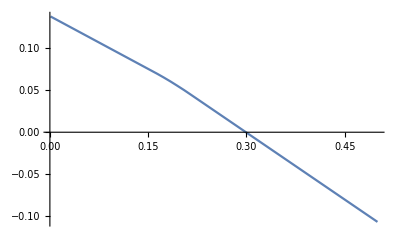

```mathematica
Plot[nxtxz[ig,ig,kkv,ig,ig,1.0,0.01][[2,1]],{kkv,0.001,.5}]
```

## Initialization

```mathematica
SetOptions[InputNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},TrackCellChangeTimes->False](*use Cell->Delete All Output*)
Switch[$System,
"Mac OS X x86 (64-bit)",SetDirectory["/Users/garyanderson/git/ProjectionMethodTools/ProjectionMethodToolsJava/code"],
"Linux x86 (64-bit)",SetDirectory["~/git/ProjectionMethodTools/ProjectisteponMethodToolsJava/code"],
"Microsoft Windows (64-bit)",SetDirectory["g:/git/ProjectionMethodTools/ProjectionMethodToolsJava/code"]];
PrependTo[$Path,"../../../AMASeriesRepresentation/AMASeriesRepresentation/"];
Get["genArbLin.mth"]
Needs["simpleRBCModel`"]
Needs["betterRBC`"]Needs["betterQuasiRBC`"];Needs["betterRSRBC`"]
```